```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
(*Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]*)
```

## Definitions

### MC Processes

#### Get interaction length

```mathematica
Clear[Getl]
Getl[mχ_,vχ_,κ_,f_,Natural_:False] := Module[{λ,λtable,mχnatconv,vχnatconv},
(*f is a log log function from kinematic variables to the inverse interaction length
κ is kinetic mixing
Natural == True is for natural units for kinematic variables ([eV] for mass and [c] for speed])*)
mχnatconv=("JpereV")/("c")^2/.Constants`SIConstRepl;
vχnatconv="c"/.Constants`SIConstRepl;
λtable = If[Natural,Table[10^f[[i]][Log10[mχ mχnatconv],Log10[vχ vχnatconv]],{i,Length[f]}],Table[10^f[[i]][Log10[mχ],Log10[vχ]],{i,Length[f]}]];
λ=(Total@λtable)^-1;

<|"l"->-(λ/κ^2)Log[1-Random[]],"λtable"->λtable|>
]
```

#### Gravitational Potential

```mathematica
Vgrav[r_]:=Piecewise[{{-(("G" "ME")/r),r>"rE"/. Constants`EarthRepl},{-(("ME" "G")/(2("rE")^3))( 3("rE")^2-r^2),r<"rE"/. Constants`EarthRepl}},-(("G" "ME")/("rE"/. Constants`EarthRepl))]/.Constants`SIConstRepl/.Constants`EarthRepl
```

#### Update velocity according to interaction length and direction of propagation

```mathematica
Clear[Updatev]
Updatev[vχ_,mχ_,r_,l_,V_]:=Module[{speed,Δt,Δr,vr,L,vp,E,reached,vrsignchanged},
speed = √(vχ . vχ);
Δt = l/speed;
Δr = Δt vχ[[1]];
E=(mχ/2)speed^2+mχ V[r];
vp = √(vχ . DiagonalMatrix[{0,1,1}] . vχ); (*Subscript[v, ⊥]^2*)
(*vr=Sqrt[(Simplify[(2/mχ)E]-2(V[Abs[r+Δr]]-V[r])-vp^2)];(*updated radial velocity*)*)
vr=Sign[vχ[[1]]]Sqrt[((2/mχ)(E-mχ (V[Abs[r+Δr]]))-vp^2)];(*updated radial velocity - kinetic energy changes by mχ(V(r)-V(r+Δr)), ie. vr is √(vr^2 + 2(V(r)-V(r+Δr)))*)

(*Print[Sqrt[((2/mχ)(E-mχ (V[r]+V[Abs[r+Δr]]))-vp^2)]];
Print[Sqrt[((2/mχ)(E-mχ (V[Abs[r+Δr]])))]];*)
reached=(1/2)speed^2-(1/2)vp^2+V[r] >V[Abs[r+Δr]];(*check that Energy is high enough to reach r+Δr*)
vrsignchanged = l > r Abs[vχ[[1]]]/vp&& vχ[[1]]<0; (*if l is greater than than this value (which corresponds to the point where the particle velocity is tangent to the surface) then the sign will change*)
(*<|"vχ"->If[reached,{vr,vχ[[2]],vχ[[3]]},{-vχ[[1]],vχ[[2]],vχ[[3]]}],"r"->Abs[r+Δr],"vr"->vr,"reached?"->reached,"E"->E,"vp"->vp,"Δr"->Δr,"Δt"->Δt,"V[r]"->V[r],"V[|r+Δr|]"->V[Abs[r+Δr]],"l"->l,"vr0"->vχ[[1]],"mχ"->N[mχ]|>*)
<|"vχ"->If[vrsignchanged,{-vr,vχ[[2]],vχ[[3]]},{vr,vχ[[2]],vχ[[3]]}],"r"->Abs[r+Δr],"vr"->vr,"reached?"->reached,"vrsignchanged"->vrsignchanged,"E"->E,"vp"->vp,"Δr"->Δr,"Δt"->Δt,"V[r]"->V[r],"V[|r+Δr|]"->V[Abs[r+Δr]],"l"->l,"vr0"->vχ[[1]],"mχ"->N[mχ]|>
]
```

```mathematica
RotateuAboutvbyϕ[u_,v_,ϕ_]:= u Cos[ϕ] + v (u . v) (1-Cos[ϕ]) - Cross[u,v] Sin[ϕ](*Rodrigues formula for rotation of u about v (unit vector) by ϕ*)
```

```mathematica
Rotatevχ[vχ_,cosθ_,mχ_,ϕ_,q_]:=Module[{vχhat, w,Δvχ,vχp},
vχhat=vχ/Sqrt[vχ . vχ];
w=Cross[vχhat,{0,1,0}];
w=w/Sqrt[w . w];
(*Print[w];*)
(*Print[vχhat];*)
Δvχ=("ℏ" q )/mχ (w Sqrt[1-cosθ^2] + vχhat cosθ)/.Constants`SIConstRepl;
(*Print[Δvχ];*)

(*Rotate about vχ by ϕ*)
vχp = vχ - RotateuAboutvbyϕ[Δvχ,vχhat,ϕ] (*negative since removing momentum*)
]
```

#### Select Interaction Process

```mathematica
σselector[σs_]:=Module[{ξ2,Ps,Psums,Nσ,n},

ξ2 = Random[];

Nσ=Length[σs];
Ps=σs/Total[σs];
Psums=Table[Sum[Ps[[i]],{i,j}],{j,Length[Ps]}];

n=0;
Do[If[ ξ2<=Psums[[i]],n=i;Break[]],{i,1,Nσ}];
(*{n,ξ2,N[Psums]}*)
n
]
```

#### Region handling

```mathematica
CrustOrCore[r_]:=Piecewise[{{1,("rcore"/.Constants`EarthRepl)<r<=("rE"/.Constants`EarthRepl)},{2,r<("rcore"/.Constants`EarthRepl)}},3](*1 => in the crust, 2 => in the core, 3 => not in the Earth*)
```

```mathematica
SortProcessesByRegion[associationlist_,key_]:=Module[{sortedlist},
sortedlist={{},{},{}}; (*1 corresponds to crust, 2 to core, 3 to outside earth (empty)*)
Do[AppendTo[sortedlist[[("region"/.associationlist[[i]])]],key/.associationlist[[i]]],{i,Length[associationlist]}];
sortedlist
]
```

### Electronic Scattering

```mathematica
Interpolateϵeuztrunced[mχ_,params_,uselog_:True,m_:40,n_:40,δ_:10^-12]:=Module[{vχmax,ωmin,ωmax,qmin,qmax,umin,umax,zmin,zmax,InterPu,InterPz,InterϵTable,Interϵf},
(*Interpolate over ϵ for electronic contribution to reduce time for a function evaluation of ϵ. We do it over the range we will be probing in the Monte-Carlo*)

(*Find the range over which we are interpolating*)
vχmax=2 10^-2 "c"/.params; (*nonrelativistic limit*)
ωmin= δ "ωedgei"/.params;
ωmax = 1/(2"ℏ") mχ vχmax^2/.params;
qmax=1/("ℏ") mχ vχmax/.params;
qmin=δ qmax;(*δ = Subscript[q, max]/Subscript[q, min] - necessary since the ϵ has a removable singularity at q=0*)

(*Now convert to u and z variables*)
umin = ωmin/( qmax "vF")/.params;
umax = Min[ωmax/(qmin "vF")/.params,10^3];(*Truncate u at a large value of ω (where we get numerical instabilities)*)
zmin = qmin/(2 "qF")/.params;
zmax = qmax/(2 "qF")/.params;

(*Log Subdivide the intervals*)
     InterPu= If[uselog,10^Subdivide[Log10[umin],Log10[umax],m],Subdivide[umin,umax,m]];
InterPz= If[uselog,10^Subdivide[Log10[zmin],Log10[zmax],n],Subdivide[zmin,zmax,n]];

InterϵTable=Table[{{InterPu[[i]],InterPz[[j]]},Abs[Im[-1/Dielectrics`ϵM[InterPu[[i]],InterPz[[j]],("νi")/(2 "qF""vF"InterPz[[j]] )]]/.params]},{i,m+1},{j,n+1}];
Interϵf=If[uselog,Interpolation[Flatten[Log10[InterϵTable],1],InterpolationOrder->4],Interpolation[Flatten[InterϵTable,1],InterpolationOrder->4]];

<|"ϵf"->Interϵf,"ϵTable"->InterϵTable,"mχ"->mχ,"vχmax"->vχmax,"us"->InterPu,"zs"->InterPz,"ωrange"->{ωmin,ωmax},"qrange"->{qmin,qmax},"urange"->{umin,umax},"zrange"->{zmin,zmax},"params"->params,"Npoints"->{m,n},"δ"->δ|>
]
```

```mathematica
dσdERdΩeofvχandϵ[ξω_,cosθ_,vχ_,κ_,ϵDict_]:=Module[{mχ,ωmax,ω,qpm,ξθ,prefactor,dσdERdΩ,loguzs},
(* Get dσ/(Subscript[dE, R]dΩ) given an interpolated ϵ dictionary. Do this as a function of dimensionless variables which will be sampled.
   ξω ∈ (0,1) - []
  cosθ ϵ (0,1) - [] negative disallowed since gas is assumed degenerate: hence no energy can be removed from the Fermi sphere.*)
mχ=ϵDict["mχ"];
ωmax =(mχ vχ^2)/(2 "ℏ")/.ϵDict["params"];
ω= (ϵDict["ωrange"][[1]]+(cosθ^2 ωmax-ϵDict["ωrange"][[1]])ξω); (*define ω in terms of ξω*)
qpm={q->(mχ vχ)/("ℏ") (cosθ-Sqrt[cosθ^2-(2ω "ℏ")/(mχ vχ^2)]),q->(mχ vχ)/("ℏ") (cosθ+Sqrt[cosθ^2-(2ω "ℏ")/(mχ vχ^2)])}/.ϵDict["params"];(*solutions for q to ω-ω(q,cosθ)=0 in the delta function that arises in the q integral. These must be summed over*)
ξθ=Sqrt[cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)]/.ϵDict["params"];(*the absolute value of the jacobian of the delta function, evaluated on the solution of q, for each of the above solutions*)

loguzs=Table[{Log10[ω/("vF"q )/.ϵDict["params"]],Log10[q/(2"qF")/.ϵDict["params"]]}/.qpm[[i]]/.ϵDict["params"],{i,2}];
prefactor=( 1/(vχ^2 "ne") 1/(("ℏ")^2 (2 π)^3) 1/ξθ (κ^2 ("e")^2)/(4 π "ϵ0") 2/(1-E^(-"β" "ℏ" ω)))/.ϵDict["params"];

dσdERdΩ =prefactor Table[10^ϵDict["ϵf"][loguzs[[i,1]],loguzs[[i,2]]],{i,2}];

<|"dσdERdΩ"->dσdERdΩ,"ω"->ω,"ωmax"->ωmax,"cosθ"->cosθ,"ξpm"->ξθ,"qpm"->qpm,"loguzs"->loguzs,"prefactor"->prefactor|>
]
```

```mathematica
Getξωandcosθ[vχ_,ϵDict_,NMax_]:=Module[{nits=0,ξs,Mξ,dσdERdΩ,ω,Accepted=False,Errors=0},
While[!Accepted,
nits+=1;
ξs={Random[],Random[]};
Mξ=NMax Random[];
(*σs=Total[dσdERdΩeofvχandϵ[ξs[[1]],ξs[[2]],vχ,1,ϵDict][["dσdERdΩ"]]];*)
{dσdERdΩ,ω}={"dσdERdΩ","ω"}/.dσdERdΩeofvχandϵ[ξs[[1]],ξs[[2]],vχ,1,ϵDict];(*Set κ to 1, overall scaling is irrelevant*)
dσdERdΩ=Total[dσdERdΩ];
Accepted=Mξ<= dσdERdΩ;
Errors=If[dσdERdΩ-NMax> 0,Break[];<|"ξω"->ξs[[1]],"cosθ"->ξs[[2]],"Mξ"->Mξ,"σs"->dσdERdΩ|>,0];
];
<|"ξω"->ξs[[1]],"ω"->ω,"cosθ"->ξs[[2]],"Mξ"->Mξ,"dσdERdΩ"->dσdERdΩ,"Max"->NMax,"Errors"->Errors,"nits"->nits|>
]
```

```mathematica
(*GetNMaxofdσdERdΩ[ϵDict_,vχ_,buffer_:1.1 ]:=Module[{},
buffer NMaximize[Total[dσdERdΩeofvχandϵ[ξω,cosθ,vχ,1,ϵDict][["dσdERdΩ"]]],{ξω,cosθ}∈Rectangle[{ϵDict["δ"]^(1/4),ϵInterpFeOsc2["δ"]^(1/4)},{1-ϵDict["δ"]^(1/4),1-ϵDict["δ"]^(1/4)}]][[1]] 
]*)
GetNMaxofdσdERdΩ[ϵDict_,vχ_,buffer_:1.1 ]:=Module[{},
(*vχmax=10^-3 "c"/.Constants`SIConstRepl;*)
buffer NMaximize[Total[dσdERdΩeofvχandϵ[ξω,cosθ,vχ,1,ϵDict][["dσdERdΩ"]]],{ξω,cosθ}∈Rectangle[{ϵDict["δ"]^(1/4),ϵDict["δ"]^(1/4)},{1-ϵDict["δ"]^(1/4),1-ϵDict["δ"]^(1/4)}]][[1]] 
]
```

### Nuclear Scattering

```mathematica
dσdΩNuc0[cosθ_,vχ_,κ_,mχ_,coeffs_,params_]:=Module[{mN,ω,qpm,ξθ,Sofqω,dσdΩ},
(* Get dσ/(dΩ) for nuclear scattering at 0 temperature. At 0 temperature there is a delta function which gives ω in terms of q (and hence cosθ through q_0)
  cosθ ϵ (0,1) - [] negative disallowed since gas is assumed 0 T: hence no energy can be removed from the nuclei.*)
mN ="mN"/. coeffs;
ω=(2 cosθ^2 mN mχ^2 vχ^2)/((mN+mχ)^2 "ℏ")/.params; (*define ω in terms of cosθ*)
qpm={q->(mχ vχ)/("ℏ") (cosθ-Sqrt[cosθ^2-(2ω "ℏ")/(mχ vχ^2)]),q->(mχ vχ)/("ℏ") (cosθ+Sqrt[cosθ^2-(2ω "ℏ")/(mχ vχ^2)])}/.params;(*solutions for q to ω-ω(q,cosθ)=0 in the delta function that arises in the q integral. These must be summed over*)
ξθ=Sqrt[cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)]/.params;(*the absolute value of the jacobian of the delta function, evaluated on the roots of q in the argument, for each of the above solutions*)

dσdΩ =Total@Table[1/(vχ^2 )  q^2/(("ℏ")^2 (2 π)^3) 1/ξθ ((κ ("e")^2)/(4 π "ϵ0" q^2))^2 FormFactors`Zeff[q,coeffs]/.qpm[[i]]/.params,{i,2}];

<|"dσdΩ"->dσdΩ,"ω"->ω,"cosθ"->cosθ,"ξpm"->ξθ,"qpm"->qpm|>
]
```

```mathematica
GetNMaxofdσdΩNuc0[vχ_,mχ_,coeffs_,params_,buffer_:1.1 ,δ_:10^-3]:=Module[{},
(*vχmax=10^-3 "c"/.Constants`SIConstRepl;*)
buffer NMaximize[Total@dσdΩNuc0[cosθ,vχ,1,mχ,coeffs,params][["dσdΩ"]],cosθ∈Interval[{δ,1-δ}]][[1]]
]
```

```mathematica
GetωandcosθNuc0[vχ_,mχ_,coeffs_,params_,NMax_]:=Module[{nits=0,cosθ,Mξ,dσdΩ,ω,Accepted=False,Errors=0},
While[!Accepted,
nits+=1;
cosθ=Random[];(*assumes 0 temp so cosθ > 0*)
Mξ=NMax Random[];
(*σs=Total[dσdERdΩeofvχandϵ[ξs[[1]],ξs[[2]],vχ,1,ϵDict][["dσdERdΩ"]]];*)
{dσdΩ,ω}={"dσdΩ","ω"}/.dσdΩNuc0[cosθ,vχ,1,mχ,coeffs,params];(*Set κ to 1, overall scaling is irrelevant*)
(*dσdΩ=Total[dσdΩ];*)
Accepted=Mξ<= dσdΩ;
Errors=If[dσdΩ-NMax> 0,Break[];True,0];
];
<|"ω"->ω,"cosθ"->cosθ,"Mξ"->Mξ,"dσdERdΩ"->dσdΩ,"Max"->NMax,"Errors"->Errors,"nits"->nits|>
]
```

### Initial Conditions

```mathematica
Getvχ∞[mχ_,βD_,maxrat_:Sqrt[50]]:=Module[{fMB,NMax,vχMax,vχMP,nits=0,vχ,P,Mξ,Accepted=False},
vχMP=Sqrt[2/(mχ βD)];(*most probable velocity in MB*)
vχMax = maxrat vχMP; (*maximum a simple rescaling of most probable, since higher velocities are exponentially suppressed*)
fMB=(#^2 E^(-βD mχ/2 #^2))&;
NMax=2/(E mχ βD);(*value of fMB at vχ MP*)
While[!Accepted && nits<30,
nits+=1;
vχ=Random[] vχMax;
(*Print[vχ];*)
Mξ=Random[]NMax;
P=fMB[vχ];(*fMB of getting velocity vχ*)
Accepted=Mξ<= P;
];
<|"vχ"->vχ,"vχMax"->vχMax,"Mξ"->Mξ,"fMB"->P,"Max"->NMax,"nits"->nits|>
]
```

```mathematica
Sample2Sphere[]:=Module[{x},
(*Point in R3, normalized gives random point on sphere or radius 1*)
x=Table[1 - 2Random[],{i,3}];
x/Sqrt[x . x]
]
```

```mathematica
GetvχatEarth[mχ_,βD_,r∞_:10^1 "rE"/.Constants`EarthRepl,V_:Vgrav]:=Module[{rE,Accepted=False,nits=0,χspeed∞,vχ∞,vperp∞,EK∞,b∞,bEarth,vrEarth,succeeded=False,vχ,χspeedEarth},

rE="rE"/.Constants`EarthRepl;

While[!Accepted &&nits<10000,
nits++;
χspeed∞="vχ"/.Getvχ∞[mχ,βD];
vχ∞= χspeed∞ Sample2Sphere[];

If[vχ∞[[1]]>0,Continue[]];(*neglect anything pointed away*)

vperp∞=Sqrt[vχ∞ . DiagonalMatrix[{0,1,1}] . vχ∞];
EK∞=1/2 mχ χspeed∞^2;
b∞=r∞ vperp∞/χspeed∞;
bEarth = b∞/Sqrt[1 + (mχ(V[r∞]-V[rE]))/EK∞];
If[bEarth<rE,succeeded=True;Break[]]
];
vrEarth = Sqrt[vχ∞[[1]]^2+2(V[r∞]-V[rE])];
(*Print[vχ∞[[1]]^2];
Print[2(V[r∞]-V[rE])];*)
vχ={-vrEarth,vχ∞[[2]],vχ∞[[3]]};
χspeedEarth = Sqrt[vχ . vχ];
<|"vχ∞"->vχ∞,"vχ"->vχ,"χspeedEarth"->χspeedEarth,"mχ"->mχ,"βD"->βD,"χspeed∞"->χspeed∞,"bEarth"->bEarth,"nits"->nits,"succeeded"->succeeded|>
]
```

### MC PreProcessing

#### Electronic

```mathematica
Clear[ProcessDataAssemblerElectronic]
(*ProcessDataAssemblerElectronic[mχ_,params_,dσdERdΩsampler_,λDict_,ProcNum_:1,uselog_:True,m_:200,n_:200,δ_:10^-7]:= Module[{ϵDict,dσdERdΩMax,dσdERdΩsample,σ},
ϵDict= Interpolateϵeuztrunced[mχ,params,uselog,m,n,δ];
dσdERdΩMax = GetNMaxofdσdERdΩ[ϵDict,#]&;
dσdERdΩsample = Getξωandcosθ[#,ϵDict,dσdERdΩMax[#]]&;
σ=1/("ne"/.λDict["fitparams"][[1]]) 10^("f"/.λDict)[Log10[mχ],Log10[#]]&;
<|"ProcNum"->ProcNum,"ϵDict"->ϵDict,"dσdERdΩMax"->dσdERdΩMax,"dσdERdΩsample"->dσdERdΩsample,"σ"->σ,"λ"->λDict["f"]|>
]*)

ProcessDataAssemblerElectronic[mχ_,params_,dσdERdΩsampler_,λDict_,RegionNum_:1,name_:"process",Save_:False,fname_:"procdata",ProcNum_:1,uselog_:True,m_:200,n_:200,δ_:10^-7]:= Module[{ϵDict,dσdERdΩMaxloglog,dσdERdΩMax,dσdERdΩsample,σ,outdict},
ϵDict= Interpolateϵeuztrunced[mχ,params,uselog,m,n,δ];
dσdERdΩMaxloglog = "Maxf"/.InterpolatedσdERdσMax[GetNMaxofdσdERdΩ[ϵDict,#]&];
dσdERdΩMax=(10^dσdERdΩMaxloglog[Log10[#]])&;
dσdERdΩsample = Getξωandcosθ[#,ϵDict,dσdERdΩMax[#]]&;
σ=1/("ne"/.λDict["fitparams"][[1]]) 10^("f"/.λDict)[Log10[mχ],Log10[#]]&;
(*we should define the fit params and f as independent variables in the module so it doesn't pass the whole expression as a hold form here*)
outdict=<|"ProcNum"->ProcNum,"ϵDict"->ϵDict,"dσdERdΩMax"->dσdERdΩMax,"dσdERdΩsample"->dσdERdΩsample,"σ"->σ,"λ"->λDict["f"],"region"->RegionNum,"mχ"->mχ,"name"->name|>;
If[Save,Utilities`SaveIt[NotebookDirectory[]<>fname,outdict]];(*Note that we have to save the object internally in the package to use it in the package. It is saved as private so can only be accessed from in here.*)
outdict 
]
```

#### Nuclear

```mathematica
VCoul[q_,params_]:= ((("e")^2)/(q^2 "ϵ0"))/.params (*no kappa included here*)
```

```mathematica
qb[sign_,mχ_,vχ_,ω_]:= ((mχ vχ + <|"+"->1,"-"->(-1)|>[[sign]] Sqrt[2 mχ (1/2 mχ vχ^2 - ω "ℏ")])/("ℏ")) (*centre of mass momentum integral bounds*)
dσdERNuc0[ω_,mχ_,vχ_,coeffs_,params_]:= 1/(2 ω ("ℏ")^3) q^2/((2 π)^2 vχ^2) VCoul[q,params]^2 FormFactors`Zeff[q,coeffs]^2 HeavisideTheta[qb["+",mχ,vχ,ω]-q]HeavisideTheta[q-qb["-",mχ,vχ,ω]]/. q -> Sqrt[((2 coeffs[["mN"]] ω)/("ℏ")) ]/.params
```

```mathematica
GetvχandξList[vχ_,n_:20,ϵ_:10^-4,uselog_:False]:=Module[{Interpointsξ},
Interpointsξ=If[uselog,10^Subdivide[Log10[ϵ],Log10[1-ϵ],n],Subdivide[ϵ,1-ϵ,n]];(*move slightly away from the boundaries so we can do a log-log interpolation (dσ/Subscript[dE, R]->0 at Subscript[ω, max], and ξ->0 at Subscript[ω, min])*)
(*Interpointsξ=10^Subdivide[Log10[ϵ],Log10[1-ϵ],n];*)
(*Interpointsξ=Subdivide[ϵ,1-ϵ,n];*)(*move slightly away from the boundaries so we can do a log-log interpolation (dσ/Subscript[dE, R]->0 at Subscript[ω, max], and ξ->0 at Subscript[ω, min])*)
Table[{vχ,Interpointsξ[[i]]},{i,n+1}]
]
```

```mathematica
ωofξ[ξ_,ωmin_,ωmax_]:=ωmin + ξ (ωmax - ωmin)
ωmaxNuc[vχ_,mχ_,mN_,params_]:= (2 vχ^2)/("ℏ") (mχ^2 mN)/(mχ + mN)^2/.params
ωofξNuc[ξ_,ωmin_,vχ_,mχ_,mN_,params_]:=ωmin + ξ (ωmaxNuc[vχ,mχ,mN,params] - ωmin)
ξofωNuc[ω_,ωmin_,vχ_,mχ_,mN_,params_]:=(ω-ωmin )/(ωmaxNuc[vχ,mχ,mN,params] - ωmin)
```

```mathematica
InterpolatevχandωσdERNucξ[mχ_:0.5 10^6 ("JpereV")/("c")^2/.Constants`SIConstRepl,FFcoeffs_,params_:Constants`SIConstRepl,vχ_:{1/10 "vesc",2 10^-1"c"}/.Constants`SIConstRepl/.Constants`EarthRepl,m_:20,n_:60,ϵ_:10^-4]:=Module[{ωmin,mN,Interpointsvχ,Interpointsvχandξ,InterdσTable,Interdσf,InterσTable,Interσf},
(*Interpolate over dσdER and σ for Nuclear contribution (to avoid doing the integral over momentum transfer at every evaluation and to speed up the numerical integration over it to find the normalization)*)

ωmin=0;
mN = "mN"/.FFcoeffs;

Interpointsvχ=10^Subdivide[Log10[vχ[[1]]],Log10[vχ[[2]]],m];
Interpointsvχandξ=SortBy[Table[GetvχandξList[Interpointsvχ[[i]],n,ϵ,True],{i,m+1}],Last];

(*Interpolate to get dσ/dER*)
InterdσTable=Table[{Interpointsvχandξ[[i,j]],dσdERNuc0[ωofξ[Interpointsvχandξ[[i,j]][[2]],ωmin,ωmaxNuc[Interpointsvχandξ[[i,j]][[1]],mχ,mN,params]],mχ,Interpointsvχandξ[[i,j]][[1]],FFcoeffs,params]},{i,m+1},{j,n+1}];
Interdσf=Interpolation[Flatten[Log10[InterdσTable],1],InterpolationOrder->4];

(*Interpolate to get σ*)
InterσTable =Table[{Interpointsvχ[[i]],("ℏ"/.params)(ωmaxNuc[Interpointsvχ[[i]],mχ,mN,params]-ωmin)NIntegrate[10^Interdσf[Log10[Interpointsvχ[[i]]],Log10[ξ]],{ξ,ϵ,1-ϵ}]},{i,m+1}]; (*The prefactor on the Integral is the Jacobian of the transformation E_R -> ξ*)
Interσf = Interpolation[Log10[InterσTable],InterpolationOrder->4];

<|"dσf"->Interdσf,"dσTable"->InterdσTable,"Interpoints"->Interpointsvχandξ,"σf"->Interσf,"σTable"->InterσTable,"Interpointsvχ"->Interpointsvχ,"mχ"->mχ,"vχ"->Log10[vχ],"ξ"->Log10[{ϵ,1-ϵ}],"NucleusParams"->FFcoeffs,"params"->params,"ωmin"->ωmin|>
]
```

```mathematica
Clear[ProcessDataAssemblerNuclear]
ProcessDataAssemblerNuclear[mχ_,coeffs_,RegionNum_:1,name_:"process",params_:Constants`SIConstRepl,Save_:False,fname_:"procdata",ProcNum_:1]:= Module[{dσdERdΩMaxloglog,dσdERdΩMax,dσdERdΩsample,σDict,σ,λinv,outdict},
	dσdERdΩMaxloglog = "Maxf"/.InterpolatedσdERdσMax[GetNMaxofdσdΩNuc0[#,mχ,coeffs,params]&];
	dσdERdΩMax=(10^dσdERdΩMaxloglog[Log10[#]])&;
	dσdERdΩsample = GetωandcosθNuc0[#,mχ,coeffs,params,dσdERdΩMax[#]]&;

     σDict=InterpolatevχandωσdERNucξ[mχ,coeffs];
	σ= 10^("σf"/.σDict)[Log10[#]]&;
    λinv=Log10[("nI"/.σDict["NucleusParams"]) σ[10^#2]]&;(*done like this to match the format used by the electronic λ inverse and Getl module*)
	outdict=<|"ProcNum"->ProcNum,"dσdERdΩMax"->dσdERdΩMax,"dσdERdΩsample"->dσdERdΩsample,"σ"->σ,"λ"->λinv,"σDict"->σDict,"region"->RegionNum,"mχ"->mχ,"name"->name|>;
	If[Save,Utilities`SaveIt[NotebookDirectory[]<>fname,outdict]];(*Note that we have to save the object internally in the package to use it in the package. It is saved as private so can only be accessed from in here.*)
outdict 
]
```

#### Process Independent

```mathematica
InterpolatedσdERdσMax[dσdERdΩMaxf_,m_:20,uselog_:True]:=Module[{vχMax,vχMin,vχs,MaxInterTable,MaxInterf},
vχMax = 2 10^-1 "c" /.Constants`SIConstRepl;
vχMin = 1/10 Constants`vescape;
vχs = N@If[uselog,10^Subdivide[Log10[vχMin],Log10[vχMax],m],Subdivide[vχMin,vχMax,m]];
MaxInterTable = Table[{vχs[[i]],dσdERdΩMaxf[vχs[[i]]]},{i,m}];
MaxInterf=If[uselog,Interpolation[Log10[MaxInterTable],InterpolationOrder->4],Interpolation[MaxInterTable,InterpolationOrder->4]];
<|"Maxf"->MaxInterf,"MaxTable"->MaxInterTable,"vχs"->vχs,"vχrange"->{vχMin,vχMax}|>
]
```

```mathematica
Clear[GetProcessData]
GetProcessData[mχ_:2]:=Module[{MeVtokg,FeDataet,SiO2Dataet,MgODataet,FeDataNuct,SiDataNuct,MgDataNuct,ODataNuct,ProcessMasterDataListt},
(*mχ - [MeV] Default value corresponds to dark electron mass for benchmark Subscript[v, D]/v ~ 4 in the MTH*)
MeVtokg = 10^6("JpereV")/("c")^2/.Constants`SIConstRepl;

(*Electronic*)
FeDataet=Table[ProcessDataAssemblerElectronic[mχ MeVtokg ,FeTotalparams[[i]],Getξωandcosθ,FeλeDictOscillators[[i]],2,ToString[StringForm["Fe ``",i]]],{i,Length[FeTotalparams]}];
SaveIt[NotebookDirectory[]<>ToString[StringForm["FeDatae_``MeV",mχ]],FeDataet];
Print["Fe e done"];

SiO2Dataet=Table[ProcessDataAssemblerElectronic[mχ MeVtokg,SiO2Totalparams[[i]],Getξωandcosθ,SiO2λeDictOscillators[[i]],1,ToString[StringForm["SiO2 ``",i]]],{i,Length[SiO2Totalparams]}];
SaveIt[NotebookDirectory[]<>ToString[StringForm["SiO2Datae_``MeV",mχ]],SiO2Dataet];
Print["SiO2 e done"];

MgODataet=Table[ProcessDataAssemblerElectronic[mχ MeVtokg,MgOTotalparams[[i]],Getξωandcosθ,MgOλeDictOscillators[[i]],1,ToString[StringForm["MgO ``",i]]],{i,Length[MgOTotalparams]}];
SaveIt[NotebookDirectory[]<>ToString[StringForm["MgODatae_``MeV",mχ]],MgODataet];
Print["MgO e done"];


(*Nuclear*)
FeDataNuct=ProcessDataAssemblerNuclear[mχ MeVtokg,FeNucCoeffs,2,"Fe Nuc"];
SaveIt[NotebookDirectory[]<>ToString[StringForm["FeDataNuc_``MeV",mχ]],FeDataNuct];
Print["Fe Nuc done"];

SiDataNuct=ProcessDataAssemblerNuclear[mχ MeVtokg,SiNucCoeffs,1,"Si Nuc"];
SaveIt[NotebookDirectory[]<>ToString[StringForm["SiDataNuc_``MeV",mχ]],SiDataNuct];
Print["Si Nuc done"];

MgDataNuct=ProcessDataAssemblerNuclear[mχ MeVtokg,MgNucCoeffs,1,"Mg Nuc"];
SaveIt[NotebookDirectory[]<>ToString[StringForm["MgDataNuc_``MeV",mχ]],MgDataNuct];
Print["Mg Nuc done"];

ODataNuct=ProcessDataAssemblerNuclear[mχ MeVtokg,ONucCoeffs,1,"O Nuc"];
SaveIt[NotebookDirectory[]<>ToString[StringForm["ODataNuc_``MeV",mχ]],ODataNuct];
Print["O Nuc done"];

(*Join into a master list*)
ProcessMasterDataListt=Join[FeDataet,SiO2Dataet,MgODataet,{FeDataNuct},{SiDataNuct},{MgDataNuct},{ODataNuct}];

SaveIt[NotebookDirectory[]<>ToString[StringForm["MasterListData_``MeV",mχ]],ProcessMasterDataListt];

ProcessMasterDataListt
]
```

#### Patch quick fix scope issue

```mathematica
(*Block[{mχ=2,MeVtokg,FeDataNuct,SiDataNuct,MgDataNuct,ODataNuct},
MeVtokg = 10^6("JpereV")/("c")^2/.Constants`SIConstRepl;
(*Nuclear*)
FeDataNuct=ProcessDataAssemblerNuclear[mχ MeVtokg,FeNucCoeffs,2,"Fe Nuc"];
SaveIt[NotebookDirectory[]<>ToString[StringForm["FeDataNuc_``MeV",mχ]],FeDataNuct];
Print["Fe Nuc done"];

SiDataNuct=ProcessDataAssemblerNuclear[mχ MeVtokg,SiNucCoeffs,1,"Si Nuc"];
SaveIt[NotebookDirectory[]<>ToString[StringForm["SiDataNuc_``MeV",mχ]],SiDataNuct];
Print["Si Nuc done"];

MgDataNuct=ProcessDataAssemblerNuclear[mχ MeVtokg,MgNucCoeffs,1,"Mg Nuc"];
SaveIt[NotebookDirectory[]<>ToString[StringForm["MgDataNuc_``MeV",mχ]],MgDataNuct];
Print["Mg Nuc done"];

ODataNuct=ProcessDataAssemblerNuclear[mχ MeVtokg,ONucCoeffs,1,"O Nuc"];
SaveIt[NotebookDirectory[]<>ToString[StringForm["ODataNuc_``MeV",mχ]],ODataNuct];
Print["O Nuc done"];
]
*)
```

General::munfl: Exp[-798.177] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-930.604] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1085.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Fe Nuc done

Si Nuc done

Mg Nuc done

O Nuc done

```mathematica
Clear[mχt,FeDataNuct,SiDataNuct,MgDataNuct,ODataNuct]
mχt=2;
MeVtokg = 10^6("JpereV")/("c")^2/.Constants`SIConstRepl;
(*Nuclear*)
FeDataNuct=ProcessDataAssemblerNuclear[mχt MeVtokg,FeNucCoeffs,2,"Fe Nuc"];
SaveIt[NotebookDirectory[]<>ToString[StringForm["FeDataNuc_``MeV",mχt]],FeDataNuct];
Print["Fe Nuc done"];

SiDataNuct=ProcessDataAssemblerNuclear[mχt MeVtokg,SiNucCoeffs,1,"Si Nuc"];
SaveIt[NotebookDirectory[]<>ToString[StringForm["SiDataNuc_``MeV",mχt]],SiDataNuct];
Print["Si Nuc done"];

MgDataNuct=ProcessDataAssemblerNuclear[mχt MeVtokg,MgNucCoeffs,1,"Mg Nuc"];
SaveIt[NotebookDirectory[]<>ToString[StringForm["MgDataNuc_``MeV",mχt]],MgDataNuct];
Print["Mg Nuc done"];

ODataNuct=ProcessDataAssemblerNuclear[mχt MeVtokg,ONucCoeffs,1,"O Nuc"];
SaveIt[NotebookDirectory[]<>ToString[StringForm["ODataNuc_``MeV",mχt]],ODataNuct];
Print["O Nuc done"];
```

General::munfl: Exp[-798.177] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-930.604] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1085.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Fe Nuc done

General::munfl: Exp[-727.398] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-848.083] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-988.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Si Nuc done

General::munfl: Exp[-822.808] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-959.322] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1118.49] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Mg Nuc done

General::munfl: Exp[-735.941] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-858.042] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1000.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

O Nuc done

```mathematica
ProcessMasterDataList2MeV[[-4]]=FeDataNuct;
ProcessMasterDataList2MeV[[-4]]
ProcessMasterDataList2MeV[[-3]]=SiDataNuct;
ProcessMasterDataList2MeV[[-2]]
ProcessMasterDataList2MeV[[-2]]=MgDataNuct;
ProcessMasterDataList2MeV[[-2]]
ProcessMasterDataList2MeV[[-1]]=ODataNuct;
ProcessMasterDataList2MeV[[-1]]
```

```mathematica
SaveIt[NotebookDirectory[]<>ToString[StringForm["MasterListData_``MeV",2]],ProcessMasterDataList2MeV]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MasterListData_2MeV.dat

### Run MC

```mathematica
Clear[RunMC]
RunMC[mχ_,κ_,vχ0_,λs_,σs_,dσdERdΩsample_,processnames_,print_:False,V_:Vgrav]:=Module[{regionindex,vχ,r,nits,ncaptured,nescaped,EventData,λtable,ProcNum,l,reached,vrsignchanged,ER,cosθ,ϕ,q,name,iscaptured},
(*
Psuedo Code
initialize cross-sections, interaction lengths, and cross-sections for each process
Get initial conditions: vχ (with perp and radial components) at earth's radius
While in the Earth
	Get interaction length in the Earth
	Update radius according to interaction length and velocity
	Update velocity according to potential change 
	select to determine which scattering process occurred
	sample to find ω and cosθ 
	update velocity
*)

{vχ,r} = {vχ0,"rE"/.Constants`EarthRepl};
regionindex=1; (*index for crust*)

(*Print[Getl[mχ,Sqrt[vχ . vχ],κ,λs[[regionindex]]]];
λtable="λtable"/.Getl[mχ,Sqrt[vχ . vχ],κ,λs[[regionindex]]];
	ProcNum=σselector[λtable];
Print[ProcNum];*)

nits=0;
ncaptured=0;
nescaped=0;
EventData = {};

While[nits<10000,
	(*nits<10000,*)
	nits++;
	If[print,
	Print["\n\nN iterations: ",nits];
	Print["vχ before propagation is ",vχ];
	];
	(*Propagate the particle*)
	(*l = Re[Getl[mχ,Sqrt[vχ . vχ],κ,λs[[ProcNum]]]]; (*this is only using one scattering process, we need all of them. *)*)
	(*l = Re[Getl[mχ,Sqrt[vχ . vχ],κ,λs[[regionindex]]]]; (*this is only using one scattering process, we need all of them. *)*)
	l = Re["l"/.Getl[mχ,Sqrt[vχ . vχ],κ,λs[[regionindex]]]]; (*this is only using one scattering process, we need all of them. *)
	
	{vχ,r,reached,vrsignchanged}={"vχ","r","reached?","vrsignchanged"}/.Updatev[vχ,mχ,r,l,V];
	regionindex=CrustOrCore[r];
	
	If[print,
	Print["l is ",l];
	Print["The r velocity changed sign: ",vrsignchanged];
	Print["vχ after propagation is ",vχ];
	Print["|vχ| is ",Sqrt[vχ . vχ]];
	Print["r is ",r];
	Print["particle is in ",{"the crust","the core","space"}[[regionindex]]];
	];
	If[r>"rE"/.Constants`EarthRepl ,nescaped++;Break[]];
	
	(*Scattering the particle*)
	(*ProcNum=σselector[Table[σs[[regionindex]][[i]][Sqrt[vχ . vχ]],{i,Length[σs[[regionindex]]]}]];*)
	λtable="λtable"/.Getl[mχ,Sqrt[vχ . vχ],κ,λs[[regionindex]]];
	ProcNum=σselector[λtable];
	name=processnames[[regionindex]][[ProcNum]];
	{ER,cosθ}={"ℏ""ω"/.Constants`SIConstRepl,"cosθ"}/.dσdERdΩsample[[regionindex]][[ProcNum]][Sqrt[vχ . vχ]];
	ϕ=2 π Random[];
	q=Sqrt[2 mχ ER ]/("ℏ")/.Constants`SIConstRepl;
	vχ = Rotatevχ[vχ,cosθ,mχ,ϕ,q];
	If[print,
	Print["(ER,cosθ,ϕ,q) is (",ER,", ",cosθ,", ",ϕ,", ",q,")"];
	];
	
	AppendTo[EventData,<|"ER"->ER,"vχ"->vχ,"|vχ|"->Sqrt[vχ . vχ],"ϕ"->ϕ,"l"->l,"cosθ"->cosθ,"q"->q,"r"->r,"Event Number"->nits,"name"->name,"ProcNum"->ProcNum,"region"->regionindex|>];
	
	iscaptured=Sqrt[vχ . vχ]<"vesc"/.Constants`EarthRepl;
	
	If[print,
	Print["Process number: ",ProcNum];
	Print["vχ after scatter is ",vχ];
	];
	
	If[iscaptured,Print["Captured with: \!\(\*SubscriptBox[\(v\), \(χ\)]\)=",Sqrt[vχ . vχ]]];
	
	(*Check if the particle is slow enough to be captured*)
	If[iscaptured,ncaptured++;Break[]];
];

(*To save we can simply add associations with event data to a list, leaving out the fixed constants at each event. *);
(*<|"ER"->ER,"vχ"->vχ,"|vχ|"->Sqrt[vχ . vχ],"ϕ"->ϕ,"l"->l,"cosθ"->cosθ,"q"->q,"r"->r,"reached?"->reached,"κ"->N@κ,"nits"->nits,"ncaptured"->ncaptured,"nescaped"->nescaped|>*)
<|"EventData"->EventData,"κ"->N@κ,"nits"->nits,"ncaptured"->ncaptured,"nescaped"->nescaped|>
]
```

```mathematica
Clear[IteratreRunMC]
IteratreRunMC[ProcAssocList_,nparticles_:10,print_:False,return_,κ_:10^-9.5,βD_:(5"JpereV"/.Constants`SIConstRepl)^-1]:=Module[{mχ,λs,σs,dσdERdΩs,processnames,ncaptured=0,nescaped=0,nended=0,EventData={},mcdict},

(*Get process and particle data*)
mχ="mχ"/.ProcAssocList;
mχ=If[Length@Union[mχ]==1,mχ[[1]],Print["mχ must be the same in all processes:",mχ];Return[<||>,Module]];

λs=SortProcessesByRegion[ProcAssocList,"λ"];
σs=SortProcessesByRegion[ProcAssocList,"σ"];
dσdERdΩs=SortProcessesByRegion[ProcAssocList,"dσdERdΩsample"];
processnames=SortProcessesByRegion[ProcAssocList,"name"];

Print[processnames];
(*Print[dσdERdΩs];*)
(*Print[Sum[dσdERdΩs[[1]][[i]][#],{i,Length[dσdERdΩs[[1]]]}]&[10^5]];*)

Monitor[
Print["\n\nMost Probable thermal velocity in the dark plasma is ",√(2/(mχ βD))," ms^-1"];
Do[
mcdict=RunMC[mχ,κ,("vχ"/.GetvχatEarth[ mχ,βD]),λs,σs,dσdERdΩs,processnames,print];
{ncaptured,nescaped}+={"ncaptured","nescaped"}/.mcdict;
If[return,AppendTo[EventData,mcdict]];
,{k,nparticles}
];
,k];

(*Show how many were captured, escaped, or maxed out number of iterations*)
nended=nparticles-(ncaptured+nescaped);
Print["ncaptured ",ncaptured];
Print["nescaped ",nescaped];
Print["nended ",nended];

If[return,EventData]
]
```

## Load

#### Load fit parameters and constants for each material

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

#### Load interaction length associations

```mathematica
FeλeDictOscillators=Table[ReadIt[NotebookDirectory[]<>ToString[StringForm["FeλeDictSIOscillator_``",i]]],{i,6}];
SiO2λeDictOscillators=Table[ReadIt[NotebookDirectory[]<>ToString[StringForm["SiO2λeDictSIOscillator_``",i]]],{i,2}];
MgOλeDictOscillators=Table[ReadIt[NotebookDirectory[]<>ToString[StringForm["MgOλeDictSIOscillator_``",i]]],{i,4}];
```

#### Load and Assemble Master Process List

```mathematica
(*FeDatae5MeV=ReadIt[NotebookDirectory[]<>"FeDatae_5MeV"];
SiO2Datae5MeV=ReadIt[NotebookDirectory[]<>"SiO2Datae_5MeV"];
MgODatae5MeV=ReadIt[NotebookDirectory[]<>"MgODatae_5MeV"];*)
```

```mathematica
(*FeDataNuc5MeV=ReadIt[NotebookDirectory[]<>"FeDataNuc_5MeV"];
SiDataNuc5MeV=ReadIt[NotebookDirectory[]<>"SiDataNuc_5MeV"];
MgDataNuc5MeV=ReadIt[NotebookDirectory[]<>"MgDataNuc_5MeV"];
ODataNuc5MeV=ReadIt[NotebookDirectory[]<>"ODataNuc_5MeV"];*)
```

```mathematica
(*ProcessMasterDataList5MeV=Join[FeDatae5MeV,SiO2Datae5MeV,MgODatae5MeV,{FeDataNuc5MeV},{SiDataNuc5MeV},{MgDataNuc5MeV},{ODataNuc5MeV}]*)
```

```mathematica
Clear[ProcessMasterDataList2MeV,ProcessMasterDataList4GeV]
ProcessMasterDataList2MeV=ReadIt[NotebookDirectory[]<>"MasterListData_2MeV"];
ProcessMasterDataList4GeV=ReadIt[NotebookDirectory[]<>"MasterListData_4000MeV"];
```

## Run PreProcesses and Interpolations

#### Run Process Data Assembler for Electronic Processes - 5 MeV

```mathematica
FeDatae=Table[ProcessDataAssemblerElectronic[10 "m"/.SIConstRepl,FeTotalparams[[i]],Getξωandcosθ,FeλeDictOscillators[[i]],2],{i,Length[FeTotalparams]}]
```

NMaximize::nnum: The function value (0.+2.04313×10^11 ⅈ) 10^(«1»)+(0.+2.04313×10^11 ⅈ) 10^(«1»[-5.14746+0.202349 ⅈ,-4.14746-0.202349 ⅈ]) is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

NMaximize::nnum: The function value (0.+2.52824×10^11 ⅈ) 10^(«1»)+(0.+2.52824×10^11 ⅈ) 10^(«1») is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

InterpolatingFunction::dmval: Input value {-1.10062,1.2617} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.3525,1.27134} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.788141,1.26083} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

NMaximize::nnum: The function value (0.+1.13072×10^11 ⅈ) 10^(InterpolatingFunction[{{-10.6665,3.},{-5.95637,1.04363}},{5,7,0,{201,201},{5,5},0,0,0,0,Automatic,«3»},«1»,{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«40392»},{-26.3832,-26.7,-26.1211,-26.1313,-25.7242,-25.7487,-25.2011,-22.9594,-24.8012,-24.6746,«40391»}},{Automatic,Automatic}][«1»,«1»])+(0.+1.13072×10^11 ⅈ) 10^(«1»[-5.3899+0.10859 ⅈ,-4.3899-0.10859 ⅈ]) is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

```mathematica
SaveIt[NotebookDirectory[]<>"FeDatae_5MeV",FeDatae]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeDatae_5MeV.dat

```mathematica
SiO2Datae=Table[ProcessDataAssemblerElectronic[10 "m"/.SIConstRepl,SiO2Totalparams[[i]],Getξωandcosθ,SiO2λeDictOscillators[[i]],1],{i,Length[SiO2Totalparams]}]
```

NMaximize::nnum: The function value (0.+1.22798×10^9 ⅈ) 10^(InterpolatingFunction[{{-9.0077,3.},{-5.94696,1.05304}},{5,7,0,{201,201},{5,5},0,0,0,0,Automatic,«3»},{{-«18»,«9»,«191»},«1»},{«1»},{Automatic,Automatic}][«1»])+(0.+1.22798×10^9 ⅈ) 10^(InterpolatingFunction[{{-9.0077,3.},{-«19»,«19»}},«3»,{«9»,«9»}][«1»]) is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

NMaximize::nnum: The function value (0.+6.09674×10^8 ⅈ) 10^(InterpolatingFunction[{{-9.0077,3.},{-5.94696,1.05304}},{5,7,0,{201,201},{5,5},0,0,0,0,Automatic,«3»},{{-«18»,«9»,«191»},«1»},{«1»},{Automatic,Automatic}][«1»])+(0.+6.09674×10^8 ⅈ) 10^(«1»[-4.87324+0.445018 ⅈ,-3.87324-«20» ⅈ]) is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

NMaximize::nnum: The function value (0.+2.52883×10^8 ⅈ) 10^(InterpolatingFunction[{{-9.0077,3.},{-5.94696,1.05304}},{5,7,0,{201,201},{5,5},0,0,0,0,Automatic,«3»},{{-«18»,«9»,«191»},«1»},{«1»},{Automatic,Automatic}][«1»])+(0.+2.52883×10^8 ⅈ) 10^(InterpolatingFunction[{{-9.0077,3.},{-«19»,«19»}},«3»,{«9»,«9»}][«1»]) is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

InterpolatingFunction::dmval: Input value {-1.29843,1.06389} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.55031,1.07353} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.98595,1.06302} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

```mathematica
SaveIt[NotebookDirectory[]<>"SiO2Datae_5MeV",SiO2Datae]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2Datae_5MeV.dat

```mathematica
MgODatae=Table[ProcessDataAssemblerElectronic[10 "m"/.SIConstRepl,MgOTotalparams[[i]],Getξωandcosθ,MgOλeDictOscillators[[i]],1],{i,Length[MgOTotalparams]}]
```

NMaximize::nnum: The function value (0.+4.02357×10^9 ⅈ) 10^(InterpolatingFunction[{{-8.92253,3.},{-5.80282,1.19718}},{5,7,0,{201,201},{5,5},0,0,0,0,Automatic,«3»},{{-«18»,«9»,«191»},{«1»}},{«1»},{Automatic,Automatic}][«1»])+(0.+4.02357×10^9 ⅈ) 10^(«1») is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

NMaximize::nnum: The function value (0.+1.96214×10^9 ⅈ) 10^(InterpolatingFunction[{{-8.92253,3.},{-5.80282,1.19718}},{5,7,0,{201,201},{5,5},0,0,0,0,Automatic,«3»},{{-«18»,«9»,«191»},{«1»}},{«1»},{Automatic,Automatic}][«1»])+(0.+1.96214×10^9 ⅈ) 10^(InterpolatingFunction[{{-8.92253,3.},{-«18»,«19»}},«3»,{«9»,«9»}][«1»]) is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

NMaximize::nnum: The function value (0.+7.93013×10^8 ⅈ) 10^(InterpolatingFunction[{{-8.92253,3.},{-5.80282,1.19718}},{5,7,0,{201,201},{5,5},0,0,0,0,Automatic,«3»},{{-«18»,«9»,«191»},{«1»}},{«1»},{Automatic,Automatic}][«1»])+(0.+7.93013×10^8 ⅈ) 10^(InterpolatingFunction[{{-8.92253,3.},{-«18»,«19»}},«3»,{«9»,«9»}][«1»]) is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-1.15429,1.20803} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.40616,1.21767} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.84181,1.20716} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

```mathematica
SaveIt[NotebookDirectory[]<>"MgODatae_5MeV",MgODatae]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgODatae_5MeV.dat

#### Run Process Data Assembler for Nuclear Processes - 5 MeV

```mathematica
FeDataNuc=ProcessDataAssemblerNuclear[10 "m"/.SIConstRepl,FeNucCoeffs,2];
```

General::munfl: Exp[-710.439] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-828.31] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-965.736] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
SiDataNuc=ProcessDataAssemblerNuclear[10 "m"/.SIConstRepl,SiNucCoeffs,1];
```

General::munfl: Exp[-754.769] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-879.994] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1026.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
MgDataNuc=ProcessDataAssemblerNuclear[10 "m"/.SIConstRepl,MgNucCoeffs,1];
```

General::munfl: Exp[-732.246] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-853.735] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-995.38] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
ODataNuc=ProcessDataAssemblerNuclear[10 "m"/.SIConstRepl,ONucCoeffs,1];
```

General::munfl: Exp[-763.496] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-890.17] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1037.86] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
SaveIt[NotebookDirectory[]<>"FeDataNuc_5MeV",FeDataNuc]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeDataNuc_5MeV.dat

```mathematica
SaveIt[NotebookDirectory[]<>"SiDataNuc_5MeV",SiDataNuc]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiDataNuc_5MeV.dat

```mathematica
SaveIt[NotebookDirectory[]<>"MgDataNuc_5MeV",MgDataNuc]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgDataNuc_5MeV.dat

```mathematica
SaveIt[NotebookDirectory[]<>"ODataNuc_5MeV",ODataNuc]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\ODataNuc_5MeV.dat

#### Run Process Data Assembler for arbitrary mass and all processes

```mathematica
ProcessMasterDataList2MeV=GetProcessData[2]
```

NMaximize::nnum: The function value (0.+1.95475×10^11 ⅈ) 10^(InterpolatingFunction[{{-9.75121,3.},{-6.15722,0.842779}},{5,7,0,{201,201},{5,5},0,0,0,0,Automatic,«3»},{{-«18»,«9»,«191»},{«1»}},{«1»},{Automatic,Automatic}][«1»])+(0.+1.95475×10^11 ⅈ) 10^(InterpolatingFunction[{{-9.75121,3.},{-«18»,«19»}},«3»,{«9»,«9»}][«1»]) is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

NMaximize::nnum: The function value (0.+6.93763×10^10 ⅈ) 10^(InterpolatingFunction[{{-9.75121,3.},{-6.15722,0.842779}},{5,7,0,{201,201},{5,5},0,0,0,0,Automatic,«3»},{{-«18»,«9»,«191»},{«1»}},{«1»},{Automatic,Automatic}][«1»])+(0.+6.93763×10^10 ⅈ) 10^(«1») is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

InterpolatingFunction::dmval: Input value {-1.10062,0.853629} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.3525,0.863275} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.788141,0.852761} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

NMaximize::nnum: The function value (0.+9.66401×10^10 ⅈ) 10^(InterpolatingFunction[{{-10.2584,3.},{-6.36444,0.635562}},{5,7,0,{201,201},{5,5},0,0,0,0,Automatic,«3»},{{-«19»,«9»,«191»},«1»},{«1»},{Automatic,Automatic}][«1»])+(0.+9.66401×10^10 ⅈ) 10^(«1») is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

General::stop: Further output of NMaximize::cvdiv will be suppressed during this calculation.

General::munfl: Exp[-798.177] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-930.604] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1085.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Takes about 13 minutes to do a preprocessing run like this.

```mathematica
ProcessMasterDataList4GeV=GetProcessData[4000]
```

InterpolatingFunction::dmval: Input value {-1.10062,4.15466} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.3525,4.16431} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.788141,4.15379} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

General::stop: Further output of NMaximize::cvdiv will be suppressed during this calculation.

NMaximize::nnum: The function value (0.+27364.3 ⅈ) 10^(InterpolatingFunction[{{-10.9967,3.},{-4.05681,2.94319}},«3»,{Automatic,«9»}][«1»])+(0.+27364.3 ⅈ) 10^(InterpolatingFunction[«1»,«3»,{«9»,«9»}][«1»]) is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

NMaximize::nnum: The function value (0.+9721.64 ⅈ) 10^(InterpolatingFunction[{{-10.9967,3.},{-4.05681,2.94319}},«3»,{Automatic,«9»}][«1»])+(0.+9721.64 ⅈ) 10^(InterpolatingFunction[«1»,«3»,{«9»,«9»}][«1»]) is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

NMaximize::nnum: The function value (0.+15.1447 ⅈ) 10^(InterpolatingFunction[{{-10.6547,3.},{-4.71816,2.28184}},«3»,{Automatic,«9»}][«1»])+(0.+15.1447 ⅈ) 10^(InterpolatingFunction[«1»][-«18»+«1»,«1»]) is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::munfl: Exp[-2.75494×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.50178×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.70609×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

< ~ 20 min for this

## Calls

#### Run 100 particles with all materials for 2 MeV and 4 GeV (MTH Benchmark)

```mathematica
IteratreRunMC[100,False,10^-9,(4"JpereV"/.Constants`SIConstRepl)^-1]
```

Most Probable thermal velocity in the dark plasma is 600000. ms^-1

ncaptured 0

nescaped 100

nended 0

took about a minute

```mathematica
IteratreRunMC[ProcessMasterDataList4GeV,100,False,10^-9,(4"JpereV"/.Constants`SIConstRepl)^-1]
```

Most Probable thermal velocity in the dark plasma is 13416.4 ms^-1

InterpolatingFunction::dmval: Input value {-26.1475,4.03612} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Captured with: v_χ=10866.6

General::munfl: Exp[-10181.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4029.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1027.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Captured with: v_χ=10968.7

Captured with: v_χ=11066.5

Captured with: v_χ=10998.4

Captured with: v_χ=9110.14

Captured with: v_χ=10954.6

Captured with: v_χ=11191.8

Captured with: v_χ=10559.2

Captured with: v_χ=11199.7

Captured with: v_χ=10707.4

Captured with: v_χ=10872.3

Captured with: v_χ=10620.5

Captured with: v_χ=10393.5

Captured with: v_χ=10899.7

Captured with: v_χ=10051.7

Captured with: v_χ=7388.28

Captured with: v_χ=10707.6

Captured with: v_χ=10904.8

Captured with: v_χ=11079.3

Captured with: v_χ=11107.7

Captured with: v_χ=11137.8

Captured with: v_χ=11188.2

Captured with: v_χ=10120.5

Captured with: v_χ=11190.3

Captured with: v_χ=10639.9

Captured with: v_χ=10225.1

Captured with: v_χ=10910.3

Captured with: v_χ=8700.68

Captured with: v_χ=9746.65

Captured with: v_χ=10700.7

Captured with: v_χ=10368.4

Captured with: v_χ=10920.3

Captured with: v_χ=10574.8

Captured with: v_χ=9761.79

Captured with: v_χ=11063.4

Captured with: v_χ=10637.7

Captured with: v_χ=11075.4

Captured with: v_χ=11020.4

Captured with: v_χ=11113.2

Captured with: v_χ=10503.8

Captured with: v_χ=10214.3

Captured with: v_χ=10656.7

Captured with: v_χ=9943.09

Captured with: v_χ=10580.1

Captured with: v_χ=10824.4

Captured with: v_χ=10639.5

Captured with: v_χ=10818.4

Captured with: v_χ=10953.8

Captured with: v_χ=11058.9

Captured with: v_χ=10619.7

Captured with: v_χ=10492.5

Captured with: v_χ=11075.4

Captured with: v_χ=11130.1

Captured with: v_χ=8988.26

Captured with: v_χ=10382.9

Captured with: v_χ=10661.9

Captured with: v_χ=10493.7

Captured with: v_χ=10686.5

Captured with: v_χ=9024.08

Captured with: v_χ=10249.6

Captured with: v_χ=10780.6

Captured with: v_χ=9673.93

Captured with: v_χ=10374.2

Captured with: v_χ=10611.3

Captured with: v_χ=11130.3

Captured with: v_χ=10958.3

Captured with: v_χ=11052.3

Captured with: v_χ=10817.6

Captured with: v_χ=10630.6

Captured with: v_χ=10744.7

Captured with: v_χ=10442.5

Captured with: v_χ=11158.4

Captured with: v_χ=10600.1

Captured with: v_χ=10978.3

Captured with: v_χ=10946.6

Captured with: v_χ=10638.6

Captured with: v_χ=11173.6

Captured with: v_χ=11175.6

Captured with: v_χ=10851.7

Captured with: v_χ=10654.7

Captured with: v_χ=10630.1

Captured with: v_χ=8978.82

Captured with: v_χ=10839.3

Captured with: v_χ=8860.99

Captured with: v_χ=10832.6

Captured with: v_χ=9680.91

Captured with: v_χ=9783.21

Captured with: v_χ=10761.5

Captured with: v_χ=10743.6

Captured with: v_χ=10950.9

Captured with: v_χ=11167.5

Captured with: v_χ=11101.7

Captured with: v_χ=10400.1

Captured with: v_χ=10836.4

Captured with: v_χ=9944.65

Captured with: v_χ=11153.2

Captured with: v_χ=10289.8

Captured with: v_χ=11087.4

Captured with: v_χ=10943.7

Captured with: v_χ=10972.2

ncaptured 100

nescaped 0

nended 0

Took about an hour

#### Run single particle for each and show printouts

```mathematica
IteratreRunMC[ProcessMasterDataList2MeV,1,True,10^-9,(4"JpereV"/.Constants`SIConstRepl)^-1]
```

Most Probable thermal velocity in the dark plasma is 600000. ms^-1

N iterations: 1

vχ before propagation is {-576477.,35898.5,-27527.9}

l is 1.29906×10^6

The r velocity changed sign: False

vχ after propagation is {-576497.,35898.5,-27527.9}

|vχ| is 578269.

r is 5.07592×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.01923×10^-28, 0.0013746, 3.03495, 507059.)

Process number: 8

vχ after scatter is {-576496.,35900.1,-27542.8}

N iterations: 2

vχ before propagation is {-576496.,35900.1,-27542.8}

l is 4.38316×10^6

The r velocity changed sign: False

vχ after propagation is {-576530.,35900.1,-27542.8}

|vχ| is 578303.

r is 706197.

particle is in the core

(ER,cosθ,ϕ,q) is (3.94971×10^-28, 0.00208127, 1.60409, 502655.)

Process number: 7

vχ after scatter is {-576529.,35914.9,-27543.2}

N iterations: 3

vχ before propagation is {-576529.,35914.9,-27543.2}

l is 583601.

The r velocity changed sign: False

vχ after propagation is {-576529.,35914.9,-27543.2}

|vχ| is 578303.

r is 124386.

particle is in the core

(ER,cosθ,ϕ,q) is (1.14125×10^-26, 0.0111875, 5.05801, 2.70195×10^6)

Process number: 7

vχ after scatter is {-576534.,35839.7,-27516.3}

N iterations: 4

vχ before propagation is {-576534.,35839.7,-27516.3}

l is 486515.

The r velocity changed sign: False

vχ after propagation is {-576534.,35839.7,-27516.3}

|vχ| is 578302.

r is 360642.

particle is in the core

(ER,cosθ,ϕ,q) is (2.129×10^-24, 0.152803, 0.690102, 3.69042×10^7)

Process number: 7

vχ after scatter is {-576365.,36516.1,-26673.8}

N iterations: 5

vχ before propagation is {-576365.,36516.1,-26673.8}

l is 1.24201×10^6

The r velocity changed sign: False

vχ after propagation is {-576364.,36516.1,-26673.8}

|vχ| is 578135.

r is 877560.

particle is in the core

(ER,cosθ,ϕ,q) is (3.40914×10^-29, 0.000611635, 3.11558, 147676.)

Process number: 7

vχ after scatter is {-576364.,36516.2,-26678.2}

N iterations: 6

vχ before propagation is {-576364.,36516.2,-26678.2}

l is 630578.

The r velocity changed sign: False

vχ after propagation is {-576365.,36516.2,-26678.2}

|vχ| is 578136.

r is 248914.

particle is in the core

(ER,cosθ,ϕ,q) is (1.83637×10^-26, 0.0141955, 2.67539, 3.42742×10^6)

Process number: 7

vχ after scatter is {-576356.,36561.7,-26768.6}

N iterations: 7

vχ before propagation is {-576356.,36561.7,-26768.6}

l is 71056.

The r velocity changed sign: False

vχ after propagation is {-576356.,36561.7,-26768.6}

|vχ| is 578135.

r is 178077.

particle is in the core

(ER,cosθ,ϕ,q) is (3.10385×10^-28, 0.00184553, 3.72089, 445592.)

Process number: 7

vχ after scatter is {-576356.,36554.4,-26779.7}

N iterations: 8

vχ before propagation is {-576356.,36554.4,-26779.7}

l is 5253.05

The r velocity changed sign: False

vχ after propagation is {-576356.,36554.4,-26779.7}

|vχ| is 578135.

r is 172840.

particle is in the core

(ER,cosθ,ϕ,q) is (1.49775×10^-24, 0.1282, 4.88682, 3.09533×10^7)

Process number: 7

vχ after scatter is {-576303.,35652.9,-26619.1}

N iterations: 9

vχ before propagation is {-576303.,35652.9,-26619.1}

l is 1.50833×10^6

The r velocity changed sign: False

vχ after propagation is {-576300.,35652.9,-26619.1}

|vχ| is 578016.

r is 1.33102×10^6

particle is in the core

(ER,cosθ,ϕ,q) is (3.82372×10^-24, 0.204882, 4.82995, 4.94573×10^7)

Process number: 7

vχ after scatter is {-576097.,34212.4,-26441.3}

N iterations: 10

vχ before propagation is {-576097.,34212.4,-26441.3}

l is 972465.

The r velocity changed sign: False

vχ after propagation is {-576099.,34212.4,-26441.3}

|vχ| is 577719.

r is 361281.

particle is in the core

(ER,cosθ,ϕ,q) is (2.21475×10^-24, 0.156008, 0.159453, 3.76401×10^7)

Process number: 7

vχ after scatter is {-575965.,34376.7,-25346.2}

N iterations: 11

vχ before propagation is {-575965.,34376.7,-25346.2}

l is 25368.6

The r velocity changed sign: False

vχ after propagation is {-575965.,34376.7,-25346.2}

|vχ| is 577546.

r is 335982.

particle is in the core

(ER,cosθ,ϕ,q) is (4.79312×10^-24, 0.229574, 1.79677, 5.53728×10^7)

Process number: 7

vχ after scatter is {-575481.,35908.1,-25683.1}

N iterations: 12

vχ before propagation is {-575481.,35908.1,-25683.1}

l is 160504.

The r velocity changed sign: False

vχ after propagation is {-575481.,35908.1,-25683.1}

|vχ| is 577172.

r is 175949.

particle is in the core

(ER,cosθ,ϕ,q) is (7.35487×10^-30, 0.000284565, 0.700426, 68592.3)

Process number: 7

vχ after scatter is {-575481.,35909.4,-25681.5}

N iterations: 13

vχ before propagation is {-575481.,35909.4,-25681.5}

l is 47029.6

The r velocity changed sign: False

vχ after propagation is {-575481.,35909.4,-25681.5}

|vχ| is 577172.

r is 129057.

particle is in the core

(ER,cosθ,ϕ,q) is (1.33506×10^-26, 0.012124, 1.44193, 2.92239×10^6)

Process number: 7

vχ after scatter is {-575475.,35995.,-25670.1}

N iterations: 14

vχ before propagation is {-575475.,35995.,-25670.1}

l is 126641.

The r velocity changed sign: False

vχ after propagation is {-575475.,35995.,-25670.1}

|vχ| is 577171.

r is 2788.33

particle is in the core

(ER,cosθ,ϕ,q) is (1.27168×10^-23, 0.374184, 2.98996, 9.01939×10^7)

Process number: 7

vχ after scatter is {-574345.,36306.3,-28072.4}

N iterations: 15

vχ before propagation is {-574345.,36306.3,-28072.4}

l is 1.47956×10^6

The r velocity changed sign: True

vχ after propagation is {574342.,36306.3,-28072.4}

|vχ| is 576173.

r is 1.47207×10^6

particle is in the core

(ER,cosθ,ϕ,q) is (8.88504×10^-28, 0.00313311, 5.6216, 753906.)

Process number: 7

vχ after scatter is {574342.,36292.6,-28090.1}

N iterations: 16

vχ before propagation is {574342.,36292.6,-28090.1}

l is 275625.

The r velocity changed sign: False

vχ after propagation is {574341.,36292.6,-28090.1}

|vχ| is 576172.

r is 1.74682×10^6

particle is in the core

(ER,cosθ,ϕ,q) is (7.55358×10^-24, 0.288884, 2.94761, 6.95126×10^7)

Process number: 7

vχ after scatter is {573819.,36634.6,-26127.}

N iterations: 17

vχ before propagation is {573819.,36634.6,-26127.}

l is 139067.

The r velocity changed sign: False

vχ after propagation is {573818.,36634.6,-26127.}

|vχ| is 575579.

r is 1.88546×10^6

particle is in the core

(ER,cosθ,ϕ,q) is (1.28854×10^-28, 0.00119438, 1.67583, 287102.)

Process number: 7

vχ after scatter is {573817.,36643.,-26126.1}

N iterations: 18

vχ before propagation is {573817.,36643.,-26126.1}

l is 844293.

The r velocity changed sign: False

vχ after propagation is {573812.,36643.,-26126.1}

|vχ| is 575574.

r is 2.72717×10^6

particle is in the core

(ER,cosθ,ϕ,q) is (5.86497×10^-24, 0.254819, 3.89883, 6.1252×10^7)

Process number: 7

vχ after scatter is {573486.,35410.3,-24834.3}

N iterations: 19

vχ before propagation is {573486.,35410.3,-24834.3}

l is 1.10767×10^6

The r velocity changed sign: False

vχ after propagation is {573476.,35410.3,-24834.3}

|vχ| is 575105.

r is 3.83171×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (6.21451×10^-27, 0.00587027, 5.53956, 1.99384×10^6)

Process number: 7

vχ after scatter is {573476.,35370.3,-24877.8}

N iterations: 20

vχ before propagation is {573476.,35370.3,-24877.8}

l is 667450.

The r velocity changed sign: False

vχ after propagation is {573469.,35370.3,-24877.8}

|vχ| is 575097.

r is 4.49727×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (6.92225×10^-24, 0.148112, 5.4068, 6.65443×10^7)

Process number: 9

vχ after scatter is {573216.,33856.6,-26116.1}

N iterations: 21

vχ before propagation is {573216.,33856.6,-26116.1}

l is 1.90422×10^6

The r velocity changed sign: False

vχ after propagation is {573188.,33856.6,-26116.1}

|vχ| is 574780.

r is 6.39621×10^6

particle is in space

ncaptured 0

nescaped 1

nended 0

```mathematica
IteratreRunMC[ProcessMasterDataList4GeV,1,True,10^-9,(4"JpereV"/.Constants`SIConstRepl)^-1]
```

Most Probable thermal velocity in the dark plasma is 13416.4 ms^-1

N iterations: 1

vχ before propagation is {-16476.3,-21.0904,320.954}

InterpolatingFunction::dmval: Input value {-26.1475,4.21694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

l is 25.5675

The r velocity changed sign: False

vχ after propagation is {-16476.3,-21.0904,320.954}

|vχ| is 16479.4

r is 6.37097×10^6

particle is in the crust

General::munfl: Exp[-6293.38] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2539.07] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1090.26] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(ER,cosθ,ϕ,q) is (6.51139×10^-23, 0.0100498, 3.43435, 9.12724×10^9)

Process number: 9

vχ after scatter is {-16477.4,-60.117,191.47}

N iterations: 2

vχ before propagation is {-16477.4,-60.117,191.47}

l is 448.822

The r velocity changed sign: False

vχ after propagation is {-16477.7,-60.117,191.47}

|vχ| is 16478.9

r is 6.37053×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (5.55368×10^-24, 0.00334146, 1.41748, 2.66559×10^9)

Process number: 8

vχ after scatter is {-16477.6,-21.0832,197.502}

N iterations: 3

vχ before propagation is {-16477.6,-21.0832,197.502}

l is 805.109

The r velocity changed sign: False

vχ after propagation is {-16478.1,-21.0832,197.502}

|vχ| is 16479.3

r is 6.36972×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.83698×10^-23, 0.00928097, 1.82999, 7.00644×10^9)

Process number: 7

vχ after scatter is {-16477.6,79.2631,170.886}

N iterations: 4

vχ before propagation is {-16477.6,79.2631,170.886}

l is 389.847

The r velocity changed sign: False

vχ after propagation is {-16477.8,79.2631,170.886}

|vχ| is 16478.9

r is 6.36933×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.22517×10^-24, 0.00223507, 0.242247, 1.68727×10^9)

Process number: 7

vχ after scatter is {-16477.5,85.2601,195.155}

N iterations: 5

vχ before propagation is {-16477.5,85.2601,195.155}

l is 645.504

The r velocity changed sign: False

vχ after propagation is {-16477.8,85.2601,195.155}

|vχ| is 16479.2

r is 6.36869×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.04762×10^-21, 0.0458922, 4.16615, 3.66105×10^10)

Process number: 8

vχ after scatter is {-16458.7,-377.91,-86.5953}

N iterations: 6

vχ before propagation is {-16458.7,-377.91,-86.5953}

l is 853.119

The r velocity changed sign: False

vχ after propagation is {-16459.2,-377.91,-86.5953}

|vχ| is 16463.8

r is 6.36783×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.18733×10^-22, 0.0209895, 3.6295, 1.67286×10^10)

Process number: 8

vχ after scatter is {-16450.2,-493.933,-305.454}

N iterations: 7

vχ before propagation is {-16450.2,-493.933,-305.454}

l is 281.863

The r velocity changed sign: False

vχ after propagation is {-16450.3,-493.933,-305.454}

|vχ| is 16460.6

r is 6.36755×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.49518×10^-23, 0.00709054, 1.71885, 5.65007×10^9)

Process number: 8

vχ after scatter is {-16452.,-411.151,-317.836}

N iterations: 8

vχ before propagation is {-16452.,-411.151,-317.836}

l is 472.854

The r velocity changed sign: False

vχ after propagation is {-16452.3,-411.151,-317.836}

|vχ| is 16460.5

r is 6.36708×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (6.85666×10^-23, 0.0103247, 3.75005, 9.3661×10^9)

Process number: 9

vχ after scatter is {-16446.7,-490.414,-431.617}

N iterations: 9

vχ before propagation is {-16446.7,-490.414,-431.617}

l is 305.171

The r velocity changed sign: False

vχ after propagation is {-16446.9,-490.414,-431.617}

|vχ| is 16459.8

r is 6.36677×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.70489×10^-25, 0.000780165, 3.63613, 5.88271×10^8)

Process number: 7

vχ after scatter is {-16446.5,-494.549,-439.284}

N iterations: 10

vχ before propagation is {-16446.5,-494.549,-439.284}

l is 153.544

The r velocity changed sign: False

vχ after propagation is {-16446.6,-494.549,-439.284}

|vχ| is 16459.9

r is 6.36662×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (8.48015×10^-24, 0.00436829, 2.3428, 3.29385×10^9)

Process number: 7

vχ after scatter is {-16446.5,-459.588,-473.34}

N iterations: 11

vχ before propagation is {-16446.5,-459.588,-473.34}

l is 797.078

The r velocity changed sign: False

vχ after propagation is {-16447.,-459.588,-473.34}

|vχ| is 16460.2

r is 6.36582×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.58829×10^-20, 0.189045, 5.27709, 1.4255×10^11)

Process number: 7

vχ after scatter is {-16031.1,-2199.88,649.094}

N iterations: 12

vχ before propagation is {-16031.1,-2199.88,649.094}

l is 1029.74

The r velocity changed sign: False

vχ after propagation is {-16031.7,-2199.88,649.094}

|vχ| is 16194.9

r is 6.3648×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.4731×10^-23, 0.00553747, 2.46981, 4.3413×10^9)

Process number: 8

vχ after scatter is {-16038.8,-2160.17,598.992}

N iterations: 13

vχ before propagation is {-16038.8,-2160.17,598.992}

l is 56.9229

The r velocity changed sign: False

vχ after propagation is {-16038.8,-2160.17,598.992}

|vχ| is 16194.7

r is 6.36475×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.15861×10^-25, 0.000856862, 2.88586, 6.35698×10^8)

Process number: 7

vχ after scatter is {-16039.5,-2157.81,589.897}

N iterations: 14

vχ before propagation is {-16039.5,-2157.81,589.897}

l is 9.42107

The r velocity changed sign: False

vχ after propagation is {-16039.5,-2157.81,589.897}

|vχ| is 16194.7

r is 6.36474×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.15024×10^-23, 0.0051708, 0.883904, 3.83617×10^9)

Process number: 7

vχ after scatter is {-16043.7,-2114.21,626.123}

N iterations: 15

vχ before propagation is {-16043.7,-2114.21,626.123}

l is 89.8565

The r velocity changed sign: False

vχ after propagation is {-16043.8,-2114.21,626.123}

|vχ| is 16194.6

r is 6.36465×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.32533×10^-21, 0.0879192, 6.10143, 6.52259×10^10)

Process number: 7

vχ after scatter is {-15900.,-2275.65,1568.11}

N iterations: 16

vχ before propagation is {-15900.,-2275.65,1568.11}

l is 1000.48

The r velocity changed sign: False

vχ after propagation is {-15900.6,-2275.65,1568.11}

|vχ| is 16139.

r is 6.36366×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.56084×10^-21, 0.0774198, 0.189848, 5.72392×10^10)

Process number: 7

vχ after scatter is {-15776.8,-2108.41,2390.33}

N iterations: 17

vχ before propagation is {-15776.8,-2108.41,2390.33}

l is 237.038

The r velocity changed sign: False

vχ after propagation is {-15776.9,-2108.41,2390.33}

|vχ| is 16095.7

r is 6.36343×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.82885×10^-25, 0.000815892, 4.62792, 6.016×10^8)

Process number: 7

vχ after scatter is {-15775.9,-2117.22,2389.41}

N iterations: 18

vχ before propagation is {-15775.9,-2117.22,2389.41}

l is 432.109

The r velocity changed sign: False

vχ after propagation is {-15776.1,-2117.22,2389.41}

|vχ| is 16095.9

r is 6.36301×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (7.23113×10^-25, 0.00123441, 5.13705, 9.61846×10^8)

Process number: 8

vχ after scatter is {-15773.6,-2130.09,2394.95}

N iterations: 19

vχ before propagation is {-15773.6,-2130.09,2394.95}

l is 69.9586

The r velocity changed sign: False

vχ after propagation is {-15773.6,-2130.09,2394.95}

|vχ| is 16096.

r is 6.36294×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.94441×10^-24, 0.00218799, 0.0338677, 1.94089×10^9)

Process number: 9

vχ after scatter is {-15769.4,-2129.12,2423.38}

N iterations: 20

vχ before propagation is {-15769.4,-2129.12,2423.38}

l is 1785.78

The r velocity changed sign: False

vχ after propagation is {-15770.4,-2129.12,2423.38}

|vχ| is 16097.

r is 6.36119×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (7.96801×10^-23, 0.013692, 3.05647, 1.00967×10^10)

Process number: 7

vχ after scatter is {-15792.7,-2116.24,2276.01}

N iterations: 21

vχ before propagation is {-15792.7,-2116.24,2276.01}

l is 114.991

The r velocity changed sign: False

vχ after propagation is {-15792.8,-2116.24,2276.01}

|vχ| is 16095.7

r is 6.36108×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.70014×10^-24, 0.00200018, 1.75758, 1.47484×10^9)

Process number: 7

vχ after scatter is {-15796.1,-2094.95,2272.39}

N iterations: 22

vχ before propagation is {-15796.1,-2094.95,2272.39}

l is 69.0666

The r velocity changed sign: False

vχ after propagation is {-15796.2,-2094.95,2272.39}

|vχ| is 16095.7

r is 6.36101×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.51093×10^-24, 0.00272004, 0.563736, 2.1194×10^9)

Process number: 8

vχ after scatter is {-15794.5,-2078.3,2298.96}

N iterations: 23

vχ before propagation is {-15794.5,-2078.3,2298.96}

l is 313.873

The r velocity changed sign: False

vχ after propagation is {-15794.7,-2078.3,2298.96}

|vχ| is 16095.8

r is 6.3607×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.5118×10^-26, 0.000325835, 5.02033, 2.40258×10^8)

Process number: 7

vχ after scatter is {-15794.1,-2081.66,2299.96}

N iterations: 24

vχ before propagation is {-15794.1,-2081.66,2299.96}

l is 919.755

The r velocity changed sign: False

vχ after propagation is {-15794.6,-2081.66,2299.96}

|vχ| is 16096.4

r is 6.3598×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.27802×10^-25, 0.000608574, 5.7, 5.3986×10^8)

Process number: 9

vχ after scatter is {-15793.1,-2086.03,2306.49}

N iterations: 25

vχ before propagation is {-15793.1,-2086.03,2306.49}

l is 975.865

The r velocity changed sign: False

vχ after propagation is {-15793.7,-2086.03,2306.49}

|vχ| is 16097.

r is 6.35884×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.70674×10^-26, 0.00020039, 4.42264, 1.4777×10^8)

Process number: 7

vχ after scatter is {-15793.5,-2088.11,2305.83}

N iterations: 26

vχ before propagation is {-15793.5,-2088.11,2305.83}

l is 3028.48

The r velocity changed sign: False

vχ after propagation is {-15795.4,-2088.11,2305.83}

|vχ| is 16098.8

r is 6.35587×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.51321×10^-22, 0.0230089, 1.1463, 1.79315×10^10)

Process number: 8

vχ after scatter is {-15804.6,-1847.31,2417.75}

N iterations: 27

vχ before propagation is {-15804.6,-1847.31,2417.75}

l is 329.961

The r velocity changed sign: False

vχ after propagation is {-15804.8,-1847.31,2417.75}

|vχ| is 16095.1

r is 6.35555×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.17422×10^-25, 0.000817898, 4.62849, 6.37266×10^8)

Process number: 8

vχ after scatter is {-15803.9,-1856.65,2416.8}

N iterations: 28

vχ before propagation is {-15803.9,-1856.65,2416.8}

l is 216.392

The r velocity changed sign: False

vχ after propagation is {-15804.,-1856.65,2416.8}

|vχ| is 16095.2

r is 6.35533×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (9.75992×10^-24, 0.00479252, 0.0872796, 3.53367×10^9)

Process number: 7

vχ after scatter is {-15796.4,-1852.09,2468.4}

N iterations: 29

vχ before propagation is {-15796.4,-1852.09,2468.4}

l is 236.396

The r velocity changed sign: False

vχ after propagation is {-15796.5,-1852.09,2468.4}

|vχ| is 16095.2

r is 6.3551×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.55517×10^-22, 0.0159022, 3.93028, 1.41056×10^10)

Process number: 9

vχ after scatter is {-15799.2,-1998.98,2319.74}

N iterations: 30

vχ before propagation is {-15799.2,-1998.98,2319.74}

l is 420.931

The r velocity changed sign: False

vχ after propagation is {-15799.4,-1998.98,2319.74}

|vχ| is 16093.4

r is 6.35469×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (7.41916×10^-25, 0.00125055, 3.02372, 9.74271×10^8)

Process number: 8

vχ after scatter is {-15801.7,-1997.29,2305.58}

N iterations: 31

vχ before propagation is {-15801.7,-1997.29,2305.58}

l is 401.121

The r velocity changed sign: False

vχ after propagation is {-15801.9,-1997.29,2305.58}

|vχ| is 16093.7

r is 6.35429×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.55138×10^-24, 0.00327305, 1.13559, 2.41309×10^9)

Process number: 7

vχ after scatter is {-15803.6,-1965.11,2321.06}

N iterations: 32

vχ before propagation is {-15803.6,-1965.11,2321.06}

l is 1186.68

The r velocity changed sign: False

vχ after propagation is {-15804.3,-1965.11,2321.06}

|vχ| is 16094.3

r is 6.35313×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.47971×10^-22, 0.0351075, 2.02588, 1.37591×10^10)

Process number: 5

vχ after scatter is {-15832.4,-1782.59,2234.67}

N iterations: 33

vχ before propagation is {-15832.4,-1782.59,2234.67}

l is 2312.65

The r velocity changed sign: False

vχ after propagation is {-15833.8,-1782.59,2234.67}

|vχ| is 16089.8

r is 6.35085×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.6064×10^-25, 0.000783441, 2.48671, 5.77462×10^8)

Process number: 7

vχ after scatter is {-15835.4,-1777.41,2228.03}

N iterations: 34

vχ before propagation is {-15835.4,-1777.41,2228.03}

l is 831.975

The r velocity changed sign: False

vχ after propagation is {-15835.9,-1777.41,2228.03}

|vχ| is 16090.3

r is 6.35003×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.85876×10^-24, 0.00301437, 3.49341, 2.22191×10^9)

Process number: 7

vχ after scatter is {-15838.8,-1788.68,2197.24}

N iterations: 35

vχ before propagation is {-15838.8,-1788.68,2197.24}

l is 269.407

The r velocity changed sign: False

vχ after propagation is {-15839.,-1788.68,2197.24}

|vχ| is 16090.4

r is 6.34977×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (9.07857×10^-24, 0.00437538, 5.77049, 3.40809×10^9)

Process number: 8

vχ after scatter is {-15830.,-1813.27,2240.42}

N iterations: 36

vχ before propagation is {-15830.,-1813.27,2240.42}

l is 827.667

The r velocity changed sign: False

vχ after propagation is {-15830.5,-1813.27,2240.42}

|vχ| is 16090.8

r is 6.34895×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (8.02518×10^-23, 0.0130084, 4.60547, 1.01328×10^10)

Process number: 8

vχ after scatter is {-15814.2,-1961.37,2221.93}

N iterations: 37

vχ before propagation is {-15814.2,-1961.37,2221.93}

l is 45.1961

The r velocity changed sign: False

vχ after propagation is {-15814.2,-1961.37,2221.93}

|vχ| is 16089.5

r is 6.34891×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.33867×10^-24, 0.00293628, 1.05754, 2.06676×10^9)

Process number: 5

vχ after scatter is {-15815.2,-1934.88,2237.26}

N iterations: 38

vχ before propagation is {-15815.2,-1934.88,2237.26}

l is 20.73

The r velocity changed sign: False

vχ after propagation is {-15815.3,-1934.88,2237.26}

|vχ| is 16089.5

r is 6.34889×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (9.86022×10^-25, 0.00126667, 4.31783, 1.12317×10^9)

Process number: 9

vχ after scatter is {-15814.3,-1950.13,2230.66}

N iterations: 39

vχ before propagation is {-15814.3,-1950.13,2230.66}

l is 138.351

The r velocity changed sign: False

vχ after propagation is {-15814.4,-1950.13,2230.66}

|vχ| is 16089.5

r is 6.34875×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.56779×10^-24, 0.00289863, 4.01512, 2.1365×10^9)

Process number: 7

vχ after scatter is {-15814.2,-1974.21,2210.11}

N iterations: 40

vχ before propagation is {-15814.2,-1974.21,2210.11}

l is 796.064

The r velocity changed sign: False

vχ after propagation is {-15814.7,-1974.21,2210.11}

|vχ| is 16090.

r is 6.34797×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (6.22895×10^-24, 0.00362431, 3.96116, 2.82299×10^9)

Process number: 8

vχ after scatter is {-15814.8,-2004.53,2181.29}

N iterations: 41

vχ before propagation is {-15814.8,-2004.53,2181.29}

l is 781.187

The r velocity changed sign: False

vχ after propagation is {-15815.3,-2004.53,2181.29}

|vχ| is 16090.3

r is 6.3472×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.40406×10^-22, 0.0158405, 3.45958, 1.34028×10^10)

Process number: 5

vχ after scatter is {-15830.3,-2065.74,1992.96}

N iterations: 42

vχ before propagation is {-15830.3,-2065.74,1992.96}

l is 2.49052

The r velocity changed sign: False

vχ after propagation is {-15830.3,-2065.74,1992.96}

|vχ| is 16088.4

r is 6.3472×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.77054×10^-22, 0.0317208, 6.15913, 2.47051×10^10)

Process number: 8

vχ after scatter is {-15767.7,-2109.15,2351.03}

N iterations: 43

vχ before propagation is {-15767.7,-2109.15,2351.03}

l is 30.1117

The r velocity changed sign: False

vχ after propagation is {-15767.8,-2109.15,2351.03}

|vχ| is 16081.

r is 6.34717×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.4298×10^-23, 0.00549413, 0.530557, 4.27702×10^9)

Process number: 8

vχ after scatter is {-15763.5,-2077.31,2405.66}

N iterations: 44

vχ before propagation is {-15763.5,-2077.31,2405.66}

l is 1112.54

The r velocity changed sign: False

vχ after propagation is {-15764.2,-2077.31,2405.66}

|vχ| is 16081.4

r is 6.34608×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.45849×10^-22, 0.0185423, 1.89829, 1.36601×10^10)

Process number: 7

vχ after scatter is {-15794.8,-1886.81,2344.48}

N iterations: 45

vχ before propagation is {-15794.8,-1886.81,2344.48}

l is 2858.89

The r velocity changed sign: False

vχ after propagation is {-15796.5,-1886.81,2344.48}

|vχ| is 16080.6

r is 6.34327×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.26951×10^-23, 0.00731475, 5.30908, 5.38851×10^9)

Process number: 7

vχ after scatter is {-15781.7,-1952.33,2387.63}

N iterations: 46

vχ before propagation is {-15781.7,-1952.33,2387.63}

l is 1013.1

The r velocity changed sign: False

vχ after propagation is {-15782.3,-1952.33,2387.63}

|vχ| is 16080.9

r is 6.34228×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.18782×10^-23, 0.00515035, 0.0570237, 5.29064×10^9)

Process number: 5

vχ after scatter is {-15770.8,-1947.85,2465.04}

N iterations: 47

vχ before propagation is {-15770.8,-1947.85,2465.04}

l is 34.9239

The r velocity changed sign: False

vχ after propagation is {-15770.8,-1947.85,2465.04}

|vχ| is 16080.7

r is 6.34224×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (5.43976×10^-22, 0.033889, 2.25703, 2.63811×10^10)

Process number: 8

vχ after scatter is {-15832.2,-1646.23,2224.09}

N iterations: 48

vχ before propagation is {-15832.2,-1646.23,2224.09}

l is 383.758

The r velocity changed sign: False

vχ after propagation is {-15832.4,-1646.23,2224.09}

|vχ| is 16072.4

r is 6.34187×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.08922×10^-25, 0.000982373, 5.21741, 7.23308×10^8)

Process number: 7

vχ after scatter is {-15830.7,-1655.56,2229.09}

N iterations: 49

vχ before propagation is {-15830.7,-1655.56,2229.09}

l is 354.129

The r velocity changed sign: False

vχ after propagation is {-15831.,-1655.56,2229.09}

|vχ| is 16072.6

r is 6.34152×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.87377×10^-24, 0.00260421, 3.63068, 1.91747×10^9)

Process number: 7

vχ after scatter is {-15833.,-1668.83,2204.05}

N iterations: 50

vχ before propagation is {-15833.,-1668.83,2204.05}

l is 356.996

The r velocity changed sign: False

vχ after propagation is {-15833.2,-1668.83,2204.05}

|vχ| is 16072.8

r is 6.34117×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (8.85278×10^-24, 0.00379937, 5.19952, 3.36544×10^9)

Process number: 9

vχ after scatter is {-15825.3,-1712.64,2226.51}

N iterations: 51

vχ before propagation is {-15825.3,-1712.64,2226.51}

l is 198.183

The r velocity changed sign: False

vχ after propagation is {-15825.4,-1712.64,2226.51}

|vχ| is 16072.8

r is 6.34097×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (6.30015×10^-24, 0.00385586, 0.467533, 2.83908×10^9)

Process number: 7

vχ after scatter is {-15822.,-1693.77,2263.96}

N iterations: 52

vχ before propagation is {-15822.,-1693.77,2263.96}

l is 187.852

The r velocity changed sign: False

vχ after propagation is {-15822.1,-1693.77,2263.96}

|vχ| is 16072.8

r is 6.34079×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.31809×10^-25, 0.000463601, 4.78022, 4.10653×10^8)

Process number: 9

vχ after scatter is {-15821.4,-1699.8,2264.28}

N iterations: 53

vχ before propagation is {-15821.4,-1699.8,2264.28}

l is 201.752

The r velocity changed sign: False

vχ after propagation is {-15821.6,-1699.8,2264.28}

|vχ| is 16072.9

r is 6.34059×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.3954×10^-22, 0.0224993, 1.27876, 1.75062×10^10)

Process number: 8

vχ after scatter is {-15831.2,-1452.23,2341.08}

N iterations: 54

vχ before propagation is {-15831.2,-1452.23,2341.08}

l is 1117.11

The r velocity changed sign: False

vχ after propagation is {-15831.9,-1452.23,2341.08}

|vχ| is 16069.8

r is 6.33949×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.8503×10^-21, 0.054938, 2.3393, 4.86546×10^10)

Process number: 9

vχ after scatter is {-15912.4,-933.235,1847.2}

N iterations: 55

vχ before propagation is {-15912.4,-933.235,1847.2}

l is 770.594

The r velocity changed sign: False

vχ after propagation is {-15912.8,-933.235,1847.2}

|vχ| is 16046.8

r is 6.33872×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.50245×10^-24, 0.00188602, 0.993369, 1.38644×10^9)

Process number: 7

vχ after scatter is {-15912.5,-916.049,1858.45}

N iterations: 56

vχ before propagation is {-15912.5,-916.049,1858.45}

l is 590.165

The r velocity changed sign: False

vχ after propagation is {-15912.9,-916.049,1858.45}

|vχ| is 16047.2

r is 6.33814×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.14011×10^-25, 0.000822944, 1.71932, 7.27794×10^8)

Process number: 9

vχ after scatter is {-15913.6,-905.401,1856.93}

N iterations: 57

vχ before propagation is {-15913.6,-905.401,1856.93}

l is 890.456

The r velocity changed sign: False

vχ after propagation is {-15914.2,-905.401,1856.93}

|vχ| is 16047.7

r is 6.33725×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.95697×10^-23, 0.00644099, 4.54681, 5.00374×10^9)

Process number: 8

vχ after scatter is {-15911.,-978.384,1844.26}

N iterations: 58

vχ before propagation is {-15911.,-978.384,1844.26}

l is 296.356

The r velocity changed sign: False

vχ after propagation is {-15911.2,-978.384,1844.26}

|vχ| is 16047.6

r is 6.33696×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.92266×10^-25, 0.000963646, 4.27646, 7.08423×10^8)

Process number: 7

vχ after scatter is {-15911.1,-987.881,1839.79}

N iterations: 59

vχ before propagation is {-15911.1,-987.881,1839.79}

l is 765.115

The r velocity changed sign: False

vχ after propagation is {-15911.6,-987.881,1839.79}

|vχ| is 16048.

r is 6.3362×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.896×10^-26, 0.00020048, 0.954481, 1.55748×10^8)

Process number: 8

vχ after scatter is {-15911.5,-986.002,1841.13}

N iterations: 60

vχ before propagation is {-15911.5,-986.002,1841.13}

l is 1051.84

The r velocity changed sign: False

vχ after propagation is {-15912.2,-986.002,1841.13}

|vχ| is 16048.7

r is 6.33516×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.34745×10^-28, 0.000026665, 3.01219, 2.35841×10^7)

Process number: 9

vχ after scatter is {-15912.2,-985.957,1840.79}

N iterations: 61

vχ before propagation is {-15912.2,-985.957,1840.79}

l is 130.676

The r velocity changed sign: False

vχ after propagation is {-15912.3,-985.957,1840.79}

|vχ| is 16048.7

r is 6.33503×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.37367×10^-20, 0.684204, 1.11427, 2.36551×10^11)

Process number: 5

vχ after scatter is {-13545.,1451.48,2701.32}

N iterations: 62

vχ before propagation is {-13545.,1451.48,2701.32}

l is 102.849

The r velocity changed sign: False

vχ after propagation is {-13545.1,1451.48,2701.32}

|vχ| is 13887.9

r is 6.33493×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.19941×10^-21, 0.089273, 4.22316, 7.32988×10^10)

Process number: 5

vχ after scatter is {-13647.8,491.712,2203.42}

N iterations: 63

vχ before propagation is {-13647.8,491.712,2203.42}

l is 177.381

The r velocity changed sign: False

vχ after propagation is {-13648.,491.712,2203.42}

|vχ| is 13833.4

r is 6.33475×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.24446×10^-22, 0.0199112, 5.6941, 1.26181×10^10)

Process number: 7

vχ after scatter is {-13623.2,387.787,2356.85}

N iterations: 64

vχ before propagation is {-13623.2,387.787,2356.85}

l is 58.9471

The r velocity changed sign: False

vχ after propagation is {-13623.2,387.787,2356.85}

|vχ| is 13831.

r is 6.3347×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (5.66353×10^-23, 0.013413, 4.28491, 8.51228×10^9)

Process number: 5

vχ after scatter is {-13633.6,273.014,2305.59}

N iterations: 65

vχ before propagation is {-13633.6,273.014,2305.59}

l is 5.8307

The r velocity changed sign: False

vχ after propagation is {-13633.6,273.014,2305.59}

|vχ| is 13829.9

r is 6.33469×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.71293×10^-22, 0.0159333, 5.87441, 1.48038×10^10)

Process number: 5

vχ after scatter is {-13598.3,185.783,2503.73}

N iterations: 66

vχ before propagation is {-13598.3,185.783,2503.73}

l is 166.513

The r velocity changed sign: False

vχ after propagation is {-13598.4,185.783,2503.73}

|vχ| is 13828.3

r is 6.33453×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (8.69142×10^-24, 0.00526399, 5.77445, 3.33463×10^9)

Process number: 7

vχ after scatter is {-13590.7,161.715,2546.18}

N iterations: 67

vχ before propagation is {-13590.7,161.715,2546.18}

l is 151.38

The r velocity changed sign: False

vχ after propagation is {-13590.8,161.715,2546.18}

|vχ| is 13828.2

r is 6.33438×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.81517×10^-21, 0.0576397, 5.74974, 4.81905×10^10)

Process number: 5

vχ after scatter is {-13441.5,-201.238,3142.71}

N iterations: 68

vχ before propagation is {-13441.5,-201.238,3142.71}

l is 23.6966

The r velocity changed sign: False

vχ after propagation is {-13441.5,-201.238,3142.71}

|vχ| is 13805.5

r is 6.33435×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.86036×10^-22, 0.0183359, 5.64684, 1.54277×10^10)

Process number: 5

vχ after scatter is {-13393.6,-336.986,3320.31}

N iterations: 69

vχ before propagation is {-13393.6,-336.986,3320.31}

l is 170.995

The r velocity changed sign: False

vχ after propagation is {-13393.8,-336.986,3320.31}

|vχ| is 13803.3

r is 6.33419×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.84195×10^-22, 0.0304125, 3.47632, 2.48893×10^10)

Process number: 5

vχ after scatter is {-13463.8,-457.772,2978.96}

N iterations: 70

vχ before propagation is {-13463.8,-457.772,2978.96}

l is 45.1349

The r velocity changed sign: False

vχ after propagation is {-13463.8,-457.772,2978.96}

|vχ| is 13797.

r is 6.33414×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.56498×10^-21, 0.151398, 3.32108, 7.64226×10^10)

Process number: 5

vχ after scatter is {-13528.,-651.8,1865.17}

N iterations: 71

vχ before propagation is {-13528.,-651.8,1865.17}

l is 69.4926

The r velocity changed sign: False

vχ after propagation is {-13528.,-651.8,1865.17}

|vχ| is 13671.5

r is 6.33408×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.59622×10^-24, 0.00284688, 3.26758, 2.14499×10^9)

Process number: 9

vχ after scatter is {-13532.,-655.785,1833.89}

N iterations: 72

vχ before propagation is {-13532.,-655.785,1833.89}

l is 78.3884

The r velocity changed sign: False

vχ after propagation is {-13532.1,-655.785,1833.89}

|vχ| is 13671.5

r is 6.334×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (7.56616×10^-25, 0.00157093, 5.60537, 9.83876×10^8)

Process number: 7

vχ after scatter is {-13530.1,-664.915,1845.08}

N iterations: 73

vχ before propagation is {-13530.1,-664.915,1845.08}

l is 11.0585

The r velocity changed sign: False

vχ after propagation is {-13530.1,-664.915,1845.08}

|vχ| is 13671.5

r is 6.33399×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (8.34462×10^-24, 0.00658314, 2.51784, 3.26743×10^9)

Process number: 5

vχ after scatter is {-13536.5,-636.655,1806.29}

N iterations: 74

vχ before propagation is {-13536.5,-636.655,1806.29}

l is 6.46642

The r velocity changed sign: False

vχ after propagation is {-13536.5,-636.655,1806.29}

|vχ| is 13671.3

r is 6.33398×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.363×10^-24, 0.00277625, 0.383594, 1.73874×10^9)

Process number: 7

vχ after scatter is {-13533.7,-627.02,1830.02}

N iterations: 75

vχ before propagation is {-13533.7,-627.02,1830.02}

l is 128.617

The r velocity changed sign: False

vχ after propagation is {-13533.8,-627.02,1830.02}

|vχ| is 13671.3

r is 6.33385×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.54136×10^-21, 0.121708, 3.907, 7.62247×10^10)

Process number: 7

vχ after scatter is {-13470.7,-1396.6,1005.75}

N iterations: 76

vχ before propagation is {-13470.7,-1396.6,1005.75}

l is 15.4908

The r velocity changed sign: False

vχ after propagation is {-13470.7,-1396.6,1005.75}

|vχ| is 13580.2

r is 6.33384×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.90055×10^-22, 0.0174193, 0.995745, 1.55935×10^10)

Process number: 5

vχ after scatter is {-13477.3,-1203.35,1132.23}

N iterations: 77

vχ before propagation is {-13477.3,-1203.35,1132.23}

l is 78.5947

The r velocity changed sign: False

vχ after propagation is {-13477.3,-1203.35,1132.23}

|vχ| is 13578.2

r is 6.33376×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (6.89258×10^-21, 0.208594, 0.856057, 9.39061×10^10)

Process number: 5

vχ after scatter is {-13205.3,-153.885,2004.44}

N iterations: 78

vχ before propagation is {-13205.3,-153.885,2004.44}

l is 22.9125

The r velocity changed sign: False

vχ after propagation is {-13205.4,-153.885,2004.44}

|vχ| is 13357.5

r is 6.33374×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.29035×10^-22, 0.0155652, 1.42018, 1.28486×10^10)

Process number: 5

vχ after scatter is {-13200.3,34.3418,2032.56}

N iterations: 79

vχ before propagation is {-13200.3,34.3418,2032.56}

l is 14.4734

The r velocity changed sign: False

vχ after propagation is {-13200.3,34.3418,2032.56}

|vχ| is 13355.9

r is 6.33372×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.25718×10^-21, 0.0549388, 5.50866, 4.01053×10^10)

Process number: 5

vχ after scatter is {-13104.5,-380.724,2446.92}

N iterations: 80

vχ before propagation is {-13104.5,-380.724,2446.92}

l is 31.0815

The r velocity changed sign: False

vχ after propagation is {-13104.6,-380.724,2446.92}

|vχ| is 13336.5

r is 6.33369×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (9.6684×10^-25, 0.00143915, 1.76955, 1.11219×10^9)

Process number: 5

vχ after scatter is {-13105.6,-364.575,2443.8}

N iterations: 81

vχ before propagation is {-13105.6,-364.575,2443.8}

l is 31.1464

The r velocity changed sign: False

vχ after propagation is {-13105.6,-364.575,2443.8}

|vχ| is 13336.5

r is 6.33366×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.243×10^-25, 0.000993399, 3.6522, 7.36782×10^8)

Process number: 5

vχ after scatter is {-13107.2,-369.908,2434.41}

N iterations: 82

vχ before propagation is {-13107.2,-369.908,2434.41}

l is 25.5869

The r velocity changed sign: False

vχ after propagation is {-13107.2,-369.908,2434.41}

|vχ| is 13336.5

r is 6.33364×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.64371×10^-23, 0.00663218, 2.82234, 4.58581×10^9)

Process number: 5

vχ after scatter is {-13119.1,-348.577,2371.01}

N iterations: 83

vχ before propagation is {-13119.1,-348.577,2371.01}

l is 52.0697

The r velocity changed sign: False

vχ after propagation is {-13119.2,-348.577,2371.01}

|vχ| is 13336.3

r is 6.33359×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.16996×10^-22, 0.0168647, 1.72544, 1.22346×10^10)

Process number: 5

vχ after scatter is {-13125.7,-169.463,2343.82}

N iterations: 84

vχ before propagation is {-13125.7,-169.463,2343.82}

l is 119.461

The r velocity changed sign: False

vχ after propagation is {-13125.8,-169.463,2343.82}

|vχ| is 13334.5

r is 6.33347×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.89522×10^-24, 0.00382196, 2.02787, 1.92461×10^9)

Process number: 5

vχ after scatter is {-13128.3,-143.873,2331.47}

N iterations: 85

vχ before propagation is {-13128.3,-143.873,2331.47}

l is 65.1656

The r velocity changed sign: False

vχ after propagation is {-13128.3,-143.873,2331.47}

|vχ| is 13334.5

r is 6.3334×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.55356×10^-25, 0.000555944, 1.86675, 4.45826×10^8)

Process number: 5

vχ after scatter is {-13128.7,-137.555,2329.58}

N iterations: 86

vχ before propagation is {-13128.7,-137.555,2329.58}

l is 64.2481

The r velocity changed sign: False

vχ after propagation is {-13128.8,-137.555,2329.58}

|vχ| is 13334.5

r is 6.33334×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.20574×10^-23, 0.00608446, 0.747998, 3.92762×10^9)

Process number: 8

vχ after scatter is {-13121.4,-97.97,2371.6}

N iterations: 87

vχ before propagation is {-13121.4,-97.97,2371.6}

l is 77.8013

The r velocity changed sign: False

vχ after propagation is {-13121.4,-97.97,2371.6}

|vχ| is 13334.4

r is 6.33326×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.0497×10^-22, 0.037352, 5.23765, 2.27622×10^10)

Process number: 5

vχ after scatter is {-13076.8,-389.475,2535.29}

N iterations: 88

vχ before propagation is {-13076.8,-389.475,2535.29}

l is 9.04538

The r velocity changed sign: False

vχ after propagation is {-13076.9,-389.475,2535.29}

|vχ| is 13326.

r is 6.33325×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.04025×10^-26, 0.0000164876, 2.35465, 1.61564×10^8)

Process number: 5

vχ after scatter is {-13077.2,-387.78,2533.64}

N iterations: 89

vχ before propagation is {-13077.2,-387.78,2533.64}

l is 4.83951

The r velocity changed sign: False

vχ after propagation is {-13077.2,-387.78,2533.64}

|vχ| is 13326.1

r is 6.33325×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.86654×10^-22, 0.0278625, 4.91732, 2.49524×10^10)

Process number: 5

vχ after scatter is {-13042.5,-749.18,2603.52}

N iterations: 90

vχ before propagation is {-13042.5,-749.18,2603.52}

l is 31.1495

The r velocity changed sign: False

vχ after propagation is {-13042.5,-749.18,2603.52}

|vχ| is 13320.9

r is 6.33322×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (8.95447×10^-22, 0.0406294, 4.86149, 3.38472×10^10)

Process number: 5

vχ after scatter is {-12980.6,-1242.8,2667.08}

N iterations: 91

vχ before propagation is {-12980.6,-1242.8,2667.08}

l is 13.17

The r velocity changed sign: False

vχ after propagation is {-12980.7,-1242.8,2667.08}

|vχ| is 13310.

r is 6.33321×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (8.99083×10^-25, 0.00127688, 4.9181, 1.07251×10^9)

Process number: 5

vχ after scatter is {-12978.6,-1258.29,2669.96}

N iterations: 92

vχ before propagation is {-12978.6,-1258.29,2669.96}

l is 19.2243

The r velocity changed sign: False

vχ after propagation is {-12978.6,-1258.29,2669.96}

|vχ| is 13310.

r is 6.33319×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (5.47715×10^-21, 0.191017, 0.887327, 8.37105×10^10)

Process number: 5

vχ after scatter is {-12680.,-296.06,3393.5}

N iterations: 93

vχ before propagation is {-12680.,-296.06,3393.5}

l is 34.673

The r velocity changed sign: False

vχ after propagation is {-12680.1,-296.06,3393.5}

|vχ| is 13129.6

r is 6.33315×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.53592×10^-21, 0.0500466, 1.74615, 4.43288×10^10)

Process number: 5

vχ after scatter is {-12692.,350.472,3278.22}

N iterations: 94

vχ before propagation is {-12692.,350.472,3278.22}

l is 1.33891

The r velocity changed sign: False

vχ after propagation is {-12692.,350.472,3278.22}

|vχ| is 13113.2

r is 6.33315×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.77554×10^-23, 0.00743899, 4.94215, 5.95904×10^9)

Process number: 5

vχ after scatter is {-12688.5,264.511,3298.1}

N iterations: 95

vχ before propagation is {-12688.5,264.511,3298.1}

l is 15.3427

The r velocity changed sign: False

vχ after propagation is {-12688.5,264.511,3298.1}

|vχ| is 13112.8

r is 6.33314×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (9.39209×10^-22, 0.044295, 0.987831, 3.46644×10^10)

Process number: 5

vχ after scatter is {-12587.1,692.345,3563.6}

N iterations: 96

vχ before propagation is {-12587.1,692.345,3563.6}

l is 71.1306

The r velocity changed sign: False

vχ after propagation is {-12587.2,692.345,3563.6}

|vχ| is 13100.2

r is 6.33307×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.01289×10^-21, 0.0990613, 1.64527, 6.20861×10^10)

Process number: 5

vχ after scatter is {-12471.7,1599.15,3460.13}

N iterations: 97

vχ before propagation is {-12471.7,1599.15,3460.13}

l is 38.8562

The r velocity changed sign: False

vχ after propagation is {-12471.8,1599.15,3460.13}

|vχ| is 13041.3

r is 6.33303×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.6577×10^-22, 0.0212281, 5.80678, 1.84398×10^10)

Process number: 5

vχ after scatter is {-12416.1,1474.11,3696.61}

N iterations: 98

vχ before propagation is {-12416.1,1474.11,3696.61}

l is 33.7077

The r velocity changed sign: False

vχ after propagation is {-12416.1,1474.11,3696.61}

|vχ| is 13038.3

r is 6.333×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (6.02259×10^-25, 0.00122161, 3.82937, 8.77797×10^8)

Process number: 9

vχ after scatter is {-12419.9,1465.9,3687.24}

N iterations: 99

vχ before propagation is {-12419.9,1465.9,3687.24}

l is 23.8001

The r velocity changed sign: False

vχ after propagation is {-12419.9,1465.9,3687.24}

|vχ| is 13038.3

r is 6.33298×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.10656×10^-24, 0.00223587, 3.507, 1.64168×10^9)

Process number: 5

vχ after scatter is {-12427.3,1457.26,3665.72}

N iterations: 100

vχ before propagation is {-12427.3,1457.26,3665.72}

l is 26.8162

The r velocity changed sign: False

vχ after propagation is {-12427.3,1457.26,3665.72}

|vχ| is 13038.3

r is 6.33295×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.09411×10^-23, 0.00493801, 4.39799, 3.74139×10^9)

Process number: 5

vχ after scatter is {-12437.5,1404.84,3650.87}

N iterations: 101

vχ before propagation is {-12437.5,1404.84,3650.87}

l is 2.97306

The r velocity changed sign: False

vχ after propagation is {-12437.5,1404.84,3650.87}

|vχ| is 13038.2

r is 6.33295×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.25987×10^-22, 0.0170609, 1.02079, 1.2696×10^10)

Process number: 5

vχ after scatter is {-12390.2,1563.91,3739.44}

N iterations: 102

vχ before propagation is {-12390.2,1563.91,3739.44}

l is 11.1235

The r velocity changed sign: False

vχ after propagation is {-12390.2,1563.91,3739.44}

|vχ| is 13036.3

r is 6.33294×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.31922×10^-23, 0.0142847, 4.84805, 6.51659×10^9)

Process number: 5

vχ after scatter is {-12396.1,1468.78,3754.86}

N iterations: 103

vχ before propagation is {-12396.1,1468.78,3754.86}

l is 16.4031

The r velocity changed sign: False

vχ after propagation is {-12396.1,1468.78,3754.86}

|vχ| is 13035.3

r is 6.33292×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.75435×10^-25, 0.00071356, 4.11263, 4.73763×10^8)

Process number: 5

vχ after scatter is {-12397.9,1463.02,3751.26}

N iterations: 104

vχ before propagation is {-12397.9,1463.02,3751.26}

l is 6.61619

The r velocity changed sign: False

vχ after propagation is {-12397.9,1463.02,3751.26}

|vχ| is 13035.3

r is 6.33292×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.90979×10^-23, 0.00860003, 2.80254, 7.07261×10^9)

Process number: 5

vχ after scatter is {-12421.9,1497.55,3655.27}

N iterations: 105

vχ before propagation is {-12421.9,1497.55,3655.27}

l is 32.9401

The r velocity changed sign: False

vχ after propagation is {-12421.9,1497.55,3655.27}

|vχ| is 13034.9

r is 6.33289×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (9.42758×10^-26, 0.0000968937, 1.50191, 3.47298×10^8)

Process number: 5

vχ after scatter is {-12421.3,1502.65,3655.44}

N iterations: 106

vχ before propagation is {-12421.3,1502.65,3655.44}

l is 6.77588

The r velocity changed sign: False

vχ after propagation is {-12421.3,1502.65,3655.44}

|vχ| is 13034.9

r is 6.33288×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.04422×10^-23, 0.00929584, 1.23702, 6.24081×10^9)

Process number: 5

vχ after scatter is {-12402.2,1589.34,3681.42}

N iterations: 107

vχ before propagation is {-12402.2,1589.34,3681.42}

l is 8.93425

The r velocity changed sign: False

vχ after propagation is {-12402.2,1589.34,3681.42}

|vχ| is 13034.4

r is 6.33287×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.27696×10^-23, 0.00676918, 6.25467, 4.04195×10^9)

Process number: 7

vχ after scatter is {-12385.,1587.59,3738.76}

N iterations: 108

vχ before propagation is {-12385.,1587.59,3738.76}

l is 1.64135

The r velocity changed sign: False

vχ after propagation is {-12385.,1587.59,3738.76}

|vχ| is 13034.1

r is 6.33287×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.57955×10^-22, 0.0230721, 3.4979, 1.81666×10^10)

Process number: 5

vχ after scatter is {-12462.9,1493.66,3498.83}

N iterations: 109

vχ before propagation is {-12462.9,1493.66,3498.83}

l is 20.0219

The r velocity changed sign: False

vχ after propagation is {-12463.,1493.66,3498.83}

|vχ| is 13030.7

r is 6.33285×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (3.9534×10^-24, 0.00276209, 6.22644, 2.24899×10^9)

Process number: 5

vχ after scatter is {-12454.1,1491.78,3530.9}

N iterations: 110

vχ before propagation is {-12454.1,1491.78,3530.9}

l is 15.4639

The r velocity changed sign: False

vχ after propagation is {-12454.1,1491.78,3530.9}

|vχ| is 13030.6

r is 6.33284×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.14465×10^-23, 0.011278, 3.12384, 7.28193×10^9)

Process number: 5

vχ after scatter is {-12482.2,1493.54,3426.73}

N iterations: 111

vχ before propagation is {-12482.2,1493.54,3426.73}

l is 6.19938

The r velocity changed sign: False

vχ after propagation is {-12482.2,1493.54,3426.73}

|vχ| is 13029.9

r is 6.33283×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.11632×10^-21, 0.0506043, 2.91968, 3.77918×10^10)

Process number: 5

vχ after scatter is {-12585.8,1612.57,2889.46}

N iterations: 112

vχ before propagation is {-12585.8,1612.57,2889.46}

l is 55.2738

The r velocity changed sign: False

vχ after propagation is {-12585.9,1612.57,2889.46}

|vχ| is 13013.6

r is 6.33278×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.01643×10^-22, 0.0380242, 3.22096, 2.26685×10^10)

Process number: 7

vχ after scatter is {-12651.6,1584.58,2561.25}

N iterations: 113

vχ before propagation is {-12651.6,1584.58,2561.25}

l is 1.92585

The r velocity changed sign: False

vχ after propagation is {-12651.6,1584.58,2561.25}

|vχ| is 13005.2

r is 6.33277×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.54886×10^-23, 0.00771169, 0.787481, 4.45152×10^9)

Process number: 5

vχ after scatter is {-12636.3,1630.9,2605.64}

N iterations: 114

vχ before propagation is {-12636.3,1630.9,2605.64}

l is 5.18199

The r velocity changed sign: False

vχ after propagation is {-12636.3,1630.9,2605.64}

|vχ| is 13004.8

r is 6.33277×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.5974×10^-22, 0.0195636, 2.35009, 1.42958×10^10)

Process number: 5

vχ after scatter is {-12643.8,1779.86,2455.22}

N iterations: 115

vχ before propagation is {-12643.8,1779.86,2455.22}

l is 13.5615

The r velocity changed sign: False

vχ after propagation is {-12643.8,1779.86,2455.22}

|vχ| is 13002.4

r is 6.33276×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.51171×10^-25, 0.000951695, 5.30141, 5.66875×10^8)

Process number: 7

vχ after scatter is {-12643.9,1772.94,2459.98}

N iterations: 116

vχ before propagation is {-12643.9,1772.94,2459.98}

l is 7.96262

The r velocity changed sign: False

vχ after propagation is {-12643.9,1772.94,2459.98}

|vχ| is 13002.4

r is 6.33275×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.46506×10^-22, 0.0169305, 2.90899, 1.36908×10^10)

Process number: 5

vχ after scatter is {-12672.,1818.79,2264.38}

N iterations: 117

vχ before propagation is {-12672.,1818.79,2264.38}

l is 0.119102

The r velocity changed sign: False

vχ after propagation is {-12672.,1818.79,2264.38}

|vχ| is 13000.6

r is 6.33275×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (4.2115×10^-23, 0.00901019, 5.20864, 7.34042×10^9)

Process number: 5

vχ after scatter is {-12675.1,1723.96,2317.54}

N iterations: 118

vχ before propagation is {-12675.1,1723.96,2317.54}

l is 32.3497

The r velocity changed sign: False

vχ after propagation is {-12675.1,1723.96,2317.54}

|vχ| is 13000.1

r is 6.33272×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.44035×10^-20, 0.428536, 5.55419, 1.35749×10^11)

Process number: 5

vχ after scatter is {-11748.8,409.737,3526.13}

N iterations: 119

vχ before propagation is {-11748.8,409.737,3526.13}

l is 5.80296

The r velocity changed sign: False

vχ after propagation is {-11748.8,409.737,3526.13}

|vχ| is 12273.4

r is 6.33271×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (5.97463×10^-25, 0.00155499, 3.42997, 8.74295×10^8)

Process number: 7

vχ after scatter is {-11752.5,406.054,3514.27}

N iterations: 120

vχ before propagation is {-11752.5,406.054,3514.27}

l is 7.39819

The r velocity changed sign: False

vχ after propagation is {-11752.5,406.054,3514.27}

|vχ| is 12273.4

r is 6.3327×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.90549×10^-21, 0.11238, 5.17841, 4.93749×10^10)

Process number: 5

vχ after scatter is {-11600.8,-245.761,3809.85}

N iterations: 121

vχ before propagation is {-11600.8,-245.761,3809.85}

l is 3.2372

The r velocity changed sign: False

vχ after propagation is {-11600.8,-245.761,3809.85}

|vχ| is 12212.8

r is 6.3327×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.23472×10^-25, 0.000479624, 4.03901, 3.97455×10^8)

Process number: 5

vχ after scatter is {-11601.8,-250.364,3806.33}

N iterations: 122

vχ before propagation is {-11601.8,-250.364,3806.33}

l is 0.375043

The r velocity changed sign: False

vχ after propagation is {-11601.8,-250.364,3806.33}

|vχ| is 12212.8

r is 6.3327×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (8.002×10^-22, 0.0483377, 2.47922, 3.19965×10^10)

Process number: 5

vχ after scatter is {-11702.1,41.2738,3446.24}

N iterations: 123

vχ before propagation is {-11702.1,41.2738,3446.24}

l is 6.33126

The r velocity changed sign: False

vχ after propagation is {-11702.1,41.2738,3446.24}

|vχ| is 12199.1

r is 6.33269×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (1.17819×10^-22, 0.045358, 2.69108, 1.22775×10^10)

Process number: 5

vχ after scatter is {-11740.2,120.378,3286.9}

N iterations: 124

vχ before propagation is {-11740.2,120.378,3286.9}

l is 2.40301

The r velocity changed sign: False

vχ after propagation is {-11740.2,120.378,3286.9}

|vχ| is 12192.2

r is 6.33269×10^6

particle is in the crust

(ER,cosθ,ϕ,q) is (2.3429×10^-20, 0.76687, 5.21447, 1.73133×10^11)

Process number: 5

vχ after scatter is {-9645.89,-1342.24,3523.39}

Captured with: v_χ=10356.6

ncaptured 1

nescaped 0

nended 0

#### Run single particle and get trajectories

```mathematica
("λ"/.ProcessMasterDataList4GeV[[-1]])[-30,5]
```

12.1183

```mathematica
IteratreRunMC[ProcessMasterDataList2MeV,1,False,True,10^-9,(4"JpereV"/.Constants`SIConstRepl)^-1]
```

Most Probable thermal velocity in the dark plasma is 600000. ms^-1

ncaptured 0

nescaped 1

nended 0

{<|EventData→{<|ER→9.67688×10^-25,vχ→{-364046.,-14741.7,33578.2},|vχ|→365889.,ϕ→0.774626,l→72716.7,cosθ→0.115112,q→2.48803×10^7,r→6.29864×10^6,Event Number→1,name→Si Nuc,ProcNum→7,region→1|>,<|ER→1.91641×10^-26,vχ→{-364058.,-14682.9,33493.1},|vχ|→365890.,ϕ→2.53858,l→102822.,cosθ→0.0150012,q→3.50132×10^6,r→6.19634×10^6,Event Number→2,name→Mg Nuc,ProcNum→8,region→1|>,<|ER→3.35702×10^-27,vχ→{-364068.,-14703.7,33530.9},|vχ|→365905.,ϕ→5.78151,l→620513.,cosθ→0.00678125,q→1.46543×10^6,r→5.57893×10^6,Event Number→3,name→Si Nuc,ProcNum→7,region→1|>,<|ER→3.87056×10^-25,vχ→{-364066.,-15049.4,33218.4},|vχ|→365888.,ϕ→3.98396,l→660942.,cosθ→0.0674116,q→1.57353×10^7,r→4.92131×10^6,Event Number→4,name→Mg Nuc,ProcNum→8,region→1|>,<|ER→8.9029×10^-27,vχ→{-364090.,-15022.8,33283.6},|vχ|→365917.,ϕ→0.384953,l→1.76258×10^6,cosθ→0.0156164,q→2.38646×10^6,r→3.1675×10^6,Event Number→5,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→3.93941×10^-30,vχ→{-364105.,-15022.4,33285.1},|vχ|→365931.,ϕ→0.239928,l→1.38235×10^6,cosθ→0.000328485,q→50199.9,r→1.79206×10^6,Event Number→6,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→8.28811×10^-26,vχ→{-364085.,-14897.1,33459.4},|vχ|→365922.,ϕ→0.619043,l→130494.,cosθ→0.047646,q→7.28141×10^6,r→1.66221×10^6,Event Number→7,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→2.81734×10^-25,vχ→{-364084.,-14975.8,33069.5},|vχ|→365890.,ϕ→3.34541,l→393567.,cosθ→0.0878472,q→1.34248×10^7,r→1.27062×10^6,Event Number→8,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→5.07132×10^-28,vχ→{-364085.,-14964.,33081.5},|vχ|→365891.,ϕ→0.775267,l→281307.,cosθ→0.00372742,q→569571.,r→990702.,Event Number→9,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.9394×10^-30,vχ→{-364087.,-14963.9,33082.5},|vχ|→365893.,ϕ→0.100566,l→674579.,cosθ→0.000230505,q→35222.6,r→319453.,Event Number→10,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→4.7421×10^-24,vχ→{-363650.,-14383.1,31620.4},|vχ|→365305.,ϕ→2.76691,l→1.44372×10^6,cosθ→0.360441,q→5.50773×10^7,r→1.11714×10^6,Event Number→11,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→3.07957×10^-27,vχ→{-363647.,-14399.8,31658.2},|vχ|→365306.,ϕ→5.86771,l→250948.,cosθ→0.0092,q→1.40357×10^6,r→867334.,Event Number→12,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→2.27637×10^-28,vχ→{-363642.,-14406.8,31667.},|vχ|→365302.,ϕ→5.6216,l→2.47031×10^6,cosθ→0.00250132,q→381601.,r→1.59176×10^6,Event Number→13,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.29816×10^-29,vχ→{-363647.,-14405.9,31664.5},|vχ|→365307.,ϕ→2.81635,l→1.15893×10^6,cosθ→0.000597317,q→91127.9,r→438100.,Event Number→14,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→3.47571×10^-25,vχ→{-363599.,-14823.3,31527.7},|vχ|→365265.,ϕ→4.40716,l→343553.,cosθ→0.0977379,q→1.49111×10^7,r→96108.7,Event Number→15,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→8.66753×10^-24,vχ→{-362515.,-13096.6,32370.9},|vχ|→364193.,ϕ→1.06462,l→51401.5,cosθ→0.488135,q→7.44621×10^7,r→44941.5,Event Number→16,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→4.59018×10^-29,vχ→{-362515.,-13092.3,32368.2},|vχ|→364192.,ϕ→2.12265,l→294946.,cosθ→0.00112664,q→171357.,r→248645.,Event Number→17,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→3.12561×10^-24,vχ→{-362062.,-12340.2,33360.8},|vχ|→363805.,ϕ→0.622562,l→277789.,cosθ→0.293992,q→4.47151×10^7,r→27863.8,Event Number→18,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→2.52651×10^-23,vχ→{-358727.,-13303.,34824.6},|vχ|→360659.,ϕ→5.73769,l→25756.4,cosθ→0.836742,q→1.2713×10^8,r→2230.78,Event Number→19,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→8.03644×10^-30,vχ→{358727.,-13300.9,34824.6},|vχ|→360659.,ϕ→1.5361,l→96245.,cosθ→0.000476031,q→71700.,r→93498.7,Event Number→20,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→4.7614×10^-27,vχ→{358725.,-13352.5,34820.7},|vχ|→360658.,ϕ→4.78197,l→19806.,cosθ→0.011587,q→1.74524×10^6,r→113199.,Event Number→21,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→9.86732×10^-27,vχ→{358719.,-13426.7,34823.9},|vχ|→360655.,ϕ→4.66393,l→725032.,cosθ→0.0166804,q→2.51239×10^6,r→834344.,Event Number→22,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.16392×10^-27,vχ→{358721.,-13412.3,34803.},|vχ|→360655.,ϕ→0.60103,l→2250.15,cosθ→0.00572886,q→862876.,r→836583.,Event Number→23,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→9.06644×10^-29,vχ→{358719.,-13408.6,34809.1},|vχ|→360653.,ϕ→2.60009,l→490835.,cosθ→0.00159893,q→240827.,r→1.32479×10^6,Event Number→24,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→4.34759×10^-26,vχ→{358698.,-13396.6,34963.6},|vχ|→360646.,ϕ→3.06608,l→177468.,cosθ→0.0350135,q→5.27365×10^6,r→1.5013×10^6,Event Number→25,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→9.03594×10^-31,vχ→{358687.,-13397.1,34963.1},|vχ|→360636.,ϕ→5.57481,l→1.19786×10^6,cosθ→0.000159631,q→24042.2,r→2.69269×10^6,Event Number→26,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.29146×10^-28,vχ→{358685.,-13401.,34970.6},|vχ|→360635.,ϕ→3.61655,l→65734.,cosθ→0.00190841,q→287428.,r→2.75806×10^6,Event Number→27,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→5.20848×10^-25,vχ→{358660.,-13574.3,34458.7},|vχ|→360568.,ϕ→5.94953,l→195108.,cosθ→0.121197,q→1.82534×10^7,r→2.95212×10^6,Event Number→28,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.16403×10^-23,vχ→{357250.,-15218.1,33092.9},|vχ|→359102.,ϕ→5.33679,l→439778.,cosθ→0.573064,q→8.6292×10^7,r→3.38957×10^6,Event Number→29,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→8.31973×10^-28,vχ→{357247.,-15214.8,33114.2},|vχ|→359101.,ϕ→2.9849,l→101533.,cosθ→0.00318472,q→729528.,r→3.49058×10^6,Event Number→30,name→Mg Nuc,ProcNum→8,region→1|>,<|ER→1.12873×10^-28,vχ→{357220.,-15212.2,33121.7},|vχ|→359075.,ϕ→2.81309,l→1.45241×10^6,cosθ→0.0012671,q→268710.,r→4.93549×10^6,Event Number→31,name→Si Nuc,ProcNum→7,region→1|>,<|ER→8.05011×10^-24,vχ→{356311.,-15195.4,35047.8},|vχ|→358353.,ϕ→3.14842,l→335049.,cosθ→0.338397,q→7.1761×10^7,r→5.26881×10^6,Event Number→32,name→Si Nuc,ProcNum→7,region→1|>,<|ER→6.37048×10^-24,vχ→{355920.,-14607.7,33289.4},|vχ|→357771.,ϕ→0.318039,l→656247.,cosθ→0.301644,q→6.38372×10^7,r→5.92132×10^6,Event Number→33,name→Si Nuc,ProcNum→7,region→1|>},κ→1.×10^-9,nits→34,ncaptured→0,nescaped→1|>}

```mathematica
eD2MeV1traj=IteratreRunMC[ProcessMasterDataList2MeV,1,False,True,10^-9,(4"JpereV"/.Constants`SIConstRepl)^-1]
```

Most Probable thermal velocity in the dark plasma is 600000. ms^-1

ncaptured 0

nescaped 1

nended 0

{<|EventData→{<|ER→4.05627×10^-28,vχ→{-420302.,12259.7,-31720.6},|vχ|→421676.,ϕ→2.49171,l→551382.,cosθ→0.00204544,q→509391.,r→5.82141×10^6,Event Number→1,name→Si Nuc,ProcNum→7,region→1|>,<|ER→1.12233×10^-24,vχ→{-420249.,12891.9,-31245.1},|vχ|→421606.,ϕ→0.934535,l→742583.,cosθ→0.107589,q→2.67946×10^7,r→5.08125×10^6,Event Number→2,name→Si Nuc,ProcNum→7,region→1|>,<|ER→5.50409×10^-23,vχ→{-415887.,16243.2,-32039.},|vχ|→417435.,ϕ→1.88089,l→212217.,cosθ→0.753587,q→1.87642×10^8,r→4.86971×10^6,Event Number→3,name→Si Nuc,ProcNum→7,region→1|>,<|ER→2.40853×10^-27,vχ→{-415908.,16278.1,-32027.5},|vχ|→417457.,ϕ→1.25638,l→1.45329×10^6,cosθ→0.00711973,q→1.24126×10^6,r→3.42181×10^6,Event Number→4,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.82343×10^-24,vχ→{-415775.,15313.8,-31753.8},|vχ|→417267.,ϕ→4.97971,l→572497.,cosθ→0.195896,q→3.41533×10^7,r→2.85144×10^6,Event Number→5,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.84583×10^-26,vχ→{-415777.,15400.6,-31700.5},|vχ|→417268.,ϕ→1.02321,l→340206.,cosθ→0.0197187,q→3.43624×10^6,r→2.51245×10^6,Event Number→6,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→5.99651×10^-31,vχ→{-415788.,15401.,-31701.},|vχ|→417279.,ϕ→2.52525,l→1.8981×10^6,cosθ→0.000112389,q→19585.6,r→621132.,Event Number→7,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→8.36669×10^-28,vχ→{-415787.,15421.3,-31708.3},|vχ|→417279.,ϕ→1.92006,l→119190.,cosθ→0.00419807,q→731584.,r→502368.,Event Number→8,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→4.53468×10^-26,vχ→{-415769.,15453.5,-31863.6},|vχ|→417275.,ϕ→2.93718,l→563100.,cosθ→0.0309062,q→5.38593×10^6,r→58718.6,Event Number→9,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.97194×10^-27,vχ→{-415768.,15486.2,-31857.5},|vχ|→417274.,ϕ→1.38781,l→402496.,cosθ→0.00644502,q→1.12314×10^6,r→342326.,Event Number→10,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→7.50642×10^-31,vχ→{-415768.,15485.6,-31857.4},|vχ|→417274.,ϕ→4.85167,l→202473.,cosθ→0.000125746,q→21913.1,r→140583.,Event Number→11,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→3.67869×10^-27,vχ→{-415762.,15525.4,-31878.9},|vχ|→417271.,ϕ→2.0703,l→1.44407×10^6,cosθ→0.00880295,q→1.53403×10^6,r→1.29827×10^6,Event Number→12,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.03543×10^-28,vχ→{-415764.,15531.6,-31883.4},|vχ|→417273.,ϕ→2.19453,l→752848.,cosθ→0.00147686,q→257364.,r→548146.,Event Number→13,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.08122×10^-26,vχ→{-415759.,15608.9,-31892.5},|vχ|→417273.,ϕ→1.69322,l→399172.,cosθ→0.0150916,q→2.62993×10^6,r→150418.,Event Number→14,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.57446×10^-26,vχ→{-415757.,15696.4,-31858.2},|vχ|→417271.,ϕ→1.20017,l→61538.4,cosθ→0.0182115,q→3.17361×10^6,r→89103.1,Event Number→15,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.16238×10^-23,vχ→{-414543.,13477.7,-32225.5},|vχ|→416013.,ϕ→4.50421,l→111002.,cosθ→0.494829,q→8.62306×10^7,r→21496.1,Event Number→16,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.97976×10^-27,vχ→{414542.,13454.,-32249.},|vχ|→416012.,ϕ→5.49582,l→561461.,cosθ→0.00647739,q→1.12537×10^6,r→537982.,Event Number→17,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→5.57678×10^-27,vχ→{414543.,13482.,-32200.6},|vχ|→416011.,ϕ→2.6178,l→204629.,cosθ→0.0108714,q→1.88877×10^6,r→741888.,Event Number→18,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→3.70798×10^-26,vχ→{414538.,13617.8,-32152.},|vχ|→416006.,ϕ→1.9102,l→131730.,cosθ→0.0280327,q→4.87031×10^6,r→873153.,Event Number→19,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.13333×10^-28,vχ→{414537.,13622.9,-32158.2},|vχ|→416006.,ϕ→0.684289,l→118268.,cosθ→0.00154981,q→269257.,r→991004.,Event Number→20,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→2.08219×10^-29,vχ→{414537.,13619.9,-32159.8},|vχ|→416006.,ϕ→5.2134,l→94604.,cosθ→0.000664294,q→115411.,r→1.08527×10^6,Event Number→21,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→5.10388×10^-26,vχ→{414531.,13763.6,-32070.4},|vχ|→415997.,ϕ→2.12388,l→536649.,cosθ→0.0328892,q→5.71397×10^6,r→1.62003×10^6,Event Number→22,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→2.06861×10^-24,vχ→{414339.,12704.,-32001.1},|vχ|→415767.,ϕ→4.66039,l→781514.,cosθ→0.209389,q→3.6377×10^7,r→2.39879×10^6,Event Number→23,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→1.65952×10^-26,vχ→{414324.,12798.9,-32018.1},|vχ|→415756.,ϕ→1.38897,l→852911.,cosθ→0.0187651,q→3.25821×10^6,r→3.24877×10^6,Event Number→24,name→Fe Nuc,ProcNum→7,region→2|>,<|ER→3.99057×10^-29,vχ→{414314.,12799.2,-32022.8},|vχ|→415746.,ϕ→0.0617278,l→748623.,cosθ→0.000602452,q→159774.,r→3.99481×10^6,Event Number→25,name→Mg Nuc,ProcNum→8,region→1|>,<|ER→5.79475×10^-24,vχ→{414000.,11724.2,-30606.4},|vχ|→415295.,ϕ→3.79436,l→462893.,cosθ→0.247969,q→6.08842×10^7,r→4.45611×10^6,Event Number→26,name→Si Nuc,ProcNum→7,region→1|>,<|ER→2.06978×10^-25,vχ→{414003.,11452.1,-30401.},|vχ|→415276.,ϕ→4.0653,l→234211.,cosθ→0.0469149,q→1.15067×10^7,r→4.68959×10^6,Event Number→27,name→Si Nuc,ProcNum→7,region→1|>,<|ER→1.56485×10^-26,vχ→{413992.,11482.3,-30489.4},|vχ|→415272.,ϕ→0.328646,l→175307.,cosθ→0.00975238,q→3.16391×10^6,r→4.86436×10^6,Event Number→28,name→O Nuc,ProcNum→9,region→1|>,<|ER→4.09074×10^-26,vχ→{413993.,11406.2,-30358.6},|vχ|→415261.,ϕ→3.66777,l→443257.,cosθ→0.0157683,q→5.11551×10^6,r→5.30625×10^6,Event Number→29,name→O Nuc,ProcNum→9,region→1|>},κ→1.×10^-9,nits→30,ncaptured→0,nescaped→1|>}

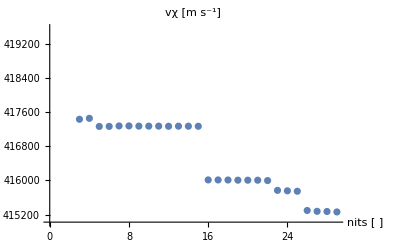

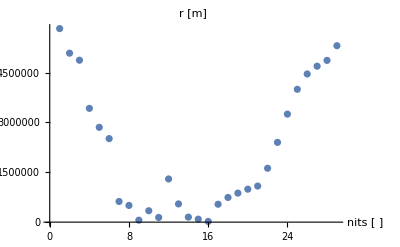

```mathematica
ListPlot[{"Event Number","|vχ|"}/.eD2MeV1traj[[1]][["EventData"]],PlotLabel->"vχ [m s^-1]",AxesLabel->{"nits [ ]"}]
ListPlot[{"Event Number","r"}/.eD2MeV1traj[[1]][["EventData"]],PlotLabel->"r [m]",AxesLabel->{"nits [ ]"}]
```

```mathematica
pD4GeV1traj=IteratreRunMC[ProcessMasterDataList4GeV,0,False,True,10^-9,(4"JpereV"/.Constants`SIConstRepl)^-1]
```

{{SiO2 1,SiO2 2,MgO 1,MgO 2,MgO 3,MgO 4,Si Nuc,Mg Nuc,O Nuc},{Fe 1,Fe 2,Fe 3,Fe 4,Fe 5,Fe 6,Fe Nuc},{}}

Most Probable thermal velocity in the dark plasma is 13416.4 ms^-1

ncaptured 0

nescaped 0

nended 0

{}

```mathematica
pD4GeV1traj=IteratreRunMC[ProcessMasterDataList4GeV,1,False,True,10^-9,(8"JpereV"/.Constants`SIConstRepl)^-1]
```

{{SiO2 1,SiO2 2,MgO 1,MgO 2,MgO 3,MgO 4,Si Nuc,Mg Nuc,O Nuc},{Fe 1,Fe 2,Fe 3,Fe 4,Fe 5,Fe 6,Fe Nuc},{}}

Most Probable thermal velocity in the dark plasma is 18973.7 ms^-1

InterpolatingFunction::dmval: Input value {-26.1475,4.04606} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ReplaceAll::reps: {ϵDict$18602252[params]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::pkspec1: The expression Piecewise[{{1, 3.486×10^6<Abs[6.371×10^6+6.04314×10^17 Re[«1»] Power[«2»] Plus[«2»]]≤6.371×10^6}, {2, Abs[6.371×10^6+6.04314×10^17 Re[«1»] Power[«2»] Plus[«2»]]<3.486×10^6}, {3, True}}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Set::shape: Lists {ER$670647,cosθ$670647} and {1.055×10^-34 ω,cosθ}/. √(If[6.04314×10^17 Re[«1»]>6.371×10^6 Abs[«1»] Power[«2»]&&-11101.2+Times[«2»]<0,{-vr$670695,{Plus[«2»],Plus[«2»],Plus[«2»]}⟦2⟧,{Plus[«2»],Plus[«2»],Plus[«2»]}⟦3⟧},{vr$670695,{Plus[«2»],Plus[«2»],Plus[«2»]}⟦2⟧,{Plus[«2»],Plus[«2»],Plus[«2»]}⟦3⟧}].If[6.04314×10^17 Re[«1»]>6.371×10^6 Abs[«1»] Power[«2»]&&-11101.2+Times[«2»]<0,{-vr$670695,«1»,«1»},{vr$670695,«1»,{Plus[«2»],Plus[«2»],Plus[«2»]}⟦3⟧}]) are not the same shape.

$Aborted